# Learning Wolfram Language

### Exercises for Section 1 | Starting Out: Elementary Arithmetic

#### 1.1 Compute1+2+3.

```mathematica
1+2+3
```

6

#### 1.2 Add the numbers 1,2,3,4,5.

```mathematica
1+2+3+4+5
```

15

#### 1.3 Multiply the numbers 1, 2, 3, 4, 5.

```mathematica
1*2*3*4*5
```

120

#### 1.4 Compute 5 squared (i . e . 5*5 or 5 raised to the power 2)

```mathematica
5^2
```

25

#### 1.5 Compute 3 raised to the fourth power .

```mathematica
3^4
```

81

#### 1.6 Compute 10 raised to the power 12 (a trillion) .

```mathematica
10^12
```

1000000000000

#### 1.7 Compute 3 raised to the power 7 x8 .

```mathematica
3^(7*8)
```

523347633027360537213511521

#### 1.8 Add parentheses to 4 - 2*3 + 4 to make 14.

```mathematica
(4-2)*(3+4)
```

14

#### 1.9 Compute twenty - nine thousand mutiplied by seventy - three .

```mathematica
29000*73
```

2117000

#### +1.1 Add all integers from - 3 to + 3.

```mathematica
-3+-2+-1+1+2+3
```

0

#### +1.2 Compute 24 divided by 3.

```mathematica
24/3
```

8

#### +1.3 Compute 5 raised to the power 100.

```mathematica
5^100
```

7888609052210118054117285652827862296732064351090230047702789306640625

#### +1.4 Subtract 5 squared from 100

```mathematica
100-(5^2)
```

75

#### +1.5 Multiply 6 by 5 squared, and add 7

```mathematica
(6*(5^2))+7
```

157

#### +1.6 Compute 3 squared minus 2 cubed .

```mathematica
(3^2)-(2^3)
```

1

#### +1.7 Compute 2 cubed times 3 squared

```mathematica
(2^3)*(3^2)
```

72

#### +1.8 Compute "double the sum of eight and negative eleven"

```mathematica
(8-11)*2
```

-6

### Exercises for Section 2 | Introducing Functions

#### 2.1 Compute 7 + 6 + 5 using the function Plus

```mathematica
Plus[7,6,5]
```

18

#### 2.2 Compute 2 x (3 + 4) using Times and Plus

```mathematica
Times[2,Plus[3,4]]
```

14

#### 2.3 Use Max to find the larger of 6x8 and 5x9

```mathematica
Max[Times[6,8],Times[5,9]]
```

48

#### 2.4 Use RandomInteger to generate a random number between 0 and 1000.

```mathematica
RandomInteger[1000]
```

443

#### 2.5 Use Plus and RandomInteger to generate a number between 10 and 20.

```mathematica
Plus[10,RandomInteger[10]]
```

12

#### +2.1 Compute 5 x4x3x2 using Times .

```mathematica
Times[5,4,3,2]
```

120

#### +2.2 Compute 2 - 3 using Subtract

```mathematica
Subtract[2,3]
```

-1

#### +2.3 Compute (8 + 7) + (9 + 2) using Times and Plus

```mathematica
Times[Plus[8,7],Plus[9,2]]
```

165

#### +2.4 Compute (26 - 89)/9 using Subtract and Divide

```mathematica
Divide[Subtract[26,89],9]
```

-7

#### +2.5 Compute 100 - 5^2 using Subtract and Power

```mathematica
Subtract[100,Power[5,2]]
```

75

#### +2.6 Find the larger of 3^5 and 5^3

```mathematica
Max[Power[3,5],Power[5,3]]
```

243

#### +2.7 Multiply 3 and the larger of 4^3 and 3^4

```mathematica
Times[3,Max[Power[4,3],Power[3,4]]]
```

243

#### +2.8 Add two random numbers each between 0 and 1000.

```mathematica
Plus[RandomInteger[1000],RandomInteger[1000]]
```

698

### Exercises for Section 3 | First Look at Lists

#### 3.1 Use Range to create the list {1, 2, 3, 4}

```mathematica
Range[4]
```

{1,2,3,4}

#### 3.2 Make a list of numbers up to 100

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

#### 3.3 Use Range and Reverse to create {4, 3, 2, 1}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

#### 3.4 Make a list of numbers from 1 to 50 in reverse order .

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

#### 3.5 Use Range, Reverse and Join to create {1, 2, 3, 4, 4, 3, 2, 1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

#### 3.6 Plot a list that counts up from 1 to 100, then down to 1.

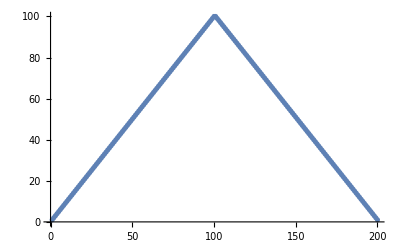

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]]
```

#### 3.7 Use Range and RandomInteger to make a list with a random lenght up to 10.

```mathematica
Range[RandomInteger[10]]
```

{1,2,3}

#### 3.8 Find a simpler form for Reverse[Reverse[Range[10]]]

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

#### 3.9 Find a simpler form to Join[{1, 2}, Join[{3, 4}, {5}]]

```mathematica
Range[5]
```

{1,2,3,4,5}

#### 3.10 Find a simpler form for Join[Range[10], Join[Range[10], Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

#### 3.11 Find a simpler form for Reverse[Join[Range[20], Reverse[Range[20]]]]

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

#### +3.1 Compute the reverse of the reverse of {1, 2, 3, 4}

```mathematica
Reverse[Reverse[Range[4]]]
```

{1,2,3,4}

#### +3.2 Use Range, Reverse and Join to create the list {1, 2, 3, 4, 5, 4, 3, 2, 1} .

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

#### +3.3 Use Range, Reverse and Join to create {3, 2, 1, 4, 3, 2, 1, 5, 4, 3, 2, 1}

```mathematica
Join[Reverse[Range[3]],Reverse[Range[4]],Reverse[Range[5]]]
```

{3,2,1,4,3,2,1,5,4,3,2,1}

#### +3.4 Plot the list numbers {10, 11, 12, 13, 14}

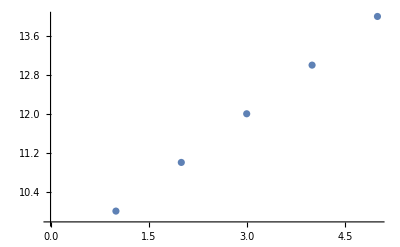

```mathematica
ListPlot[Range[10,14]]
```

### Exercises for Section 4 | Displaying Lists

#### 4.1 Make a bar chart of {1, 1, 2, 3, 5}

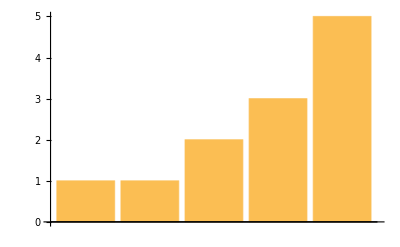

```mathematica
BarChart[{1,1,2,3,5}]
```

#### 4.2 Make a pie chart of numbers from 1 to 10.

```mathematica
PieChart[Range[10]]
```

-Graphics-

#### 4.3 Make a bar chart of numbers counting down from 20 to 1.

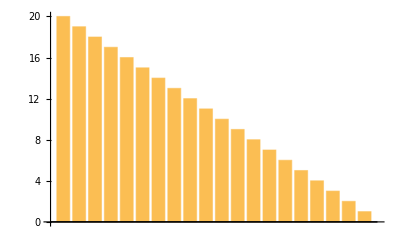

```mathematica
BarChart[Reverse[Range[20]]]
```

#### 4.4 Display numbers from 1 to 5 in a column .

```mathematica
Column[Range[5]]
```

1
2
3
4
5

#### 4.5 Make a number line plot of the squares {1, 4, 9, 16, 25} .

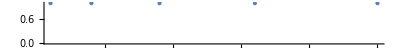

```mathematica
NumberLinePlot[Range[5]^2]
```

#### 4.6 Make a pie chart with 10 identical segments, each of size 1.

```mathematica
PieChart[ConstantArray[1,10]]
```

-Graphics-

#### 4.7 Make a column of pie charts with 1, 2 and 3 identical segments.

```mathematica
Column[{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]},3]
```

-Graphics-

#### +4.1 Make a list of pie charts with 1, 2 and 3 identical segments .

```mathematica
{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

#### +4.2 Make a bar chart of the sequence 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1.

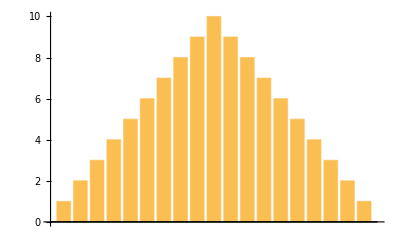

```mathematica
BarChart[Join[Range[10],Reverse[Range[9]]]]
```

#### +4.3 Make a list of pie chart, bar chart and line plot of the numbers from 1 to 10.

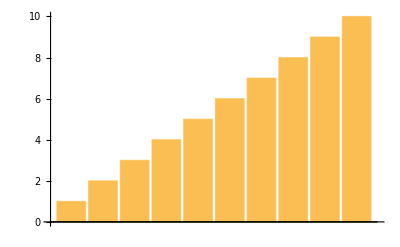
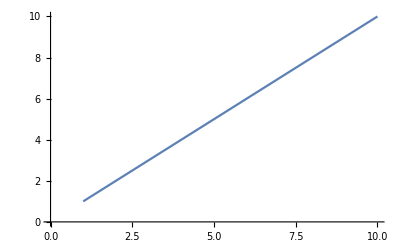
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{PieChart[Range[10]],BarChart[Range[10]],ListLinePlot[Range[10]]}
```

#### +4.4 Make a list of a pie chart and a bar chart of {1, 1, 2, 3, 5, 8, 13, 21, 34, 55}

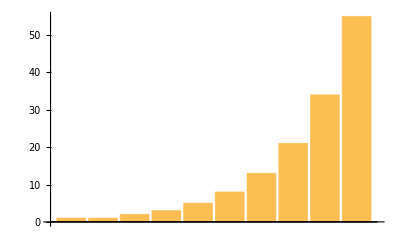
{-Graphics-,-Graphics-}

```mathematica
{PieChart[Fibonacci[Range[10]]],BarChart[Fibonacci[Range[10]]]}
```

#### +4.5 Make a column of two number line plot of {1, 2, 3, 4, 5}

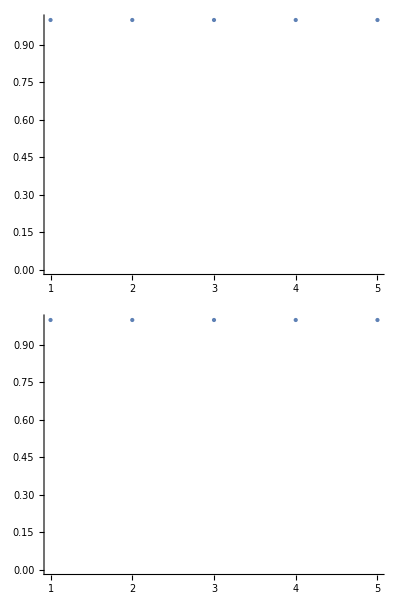

```mathematica
Column[{NumberLinePlot[Range[5]],NumberLinePlot[Range[5]]}]
```

#### +4.6 Mae a number line of fractions 1/2, 1/3, ... through 1/9.

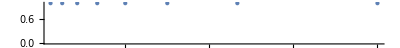

```mathematica
NumberLinePlot[{ConstantArray[1,8]/Range[2,9]}]
```

### Exercises for Section 5 | Operations on Lists

#### 5.1 Make a list of the first 10 squares, in reverse order .

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

#### 5.2 Find the total of the first 10 squares .

```mathematica
Total[Reverse[Range[10]^2]]
```

385

#### 5.3 Make a plot of the first 10 squares, starting at 1.

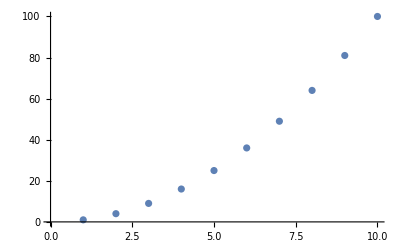

```mathematica
ListPlot[Range[10]^2]
```

#### 5.4 Use Sort, Join and Range to create {1, 1, 2, 2, 3, 3, 4, 4}.

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

#### 5.5 Use Range and + to make a list of numbers from 10 to 20, inclusive .

```mathematica
Range[0,10]+10
```

{10,11,12,13,14,15,16,17,18,19,20}

#### 5.6 Make a combined list of the first 5 squares and cubes (numbers raised to the power 3), sorted into order .

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

#### 5.7 Find the number of digits in 2^128.

```mathematica
Length[IntegerDigits[2^128]]
```

39

#### 5.8 Find the first digit of 3^32

```mathematica
First[IntegerDigits[2^32]]
```

4

#### 5.9 Find the first 10 digits in 2^100.

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

#### 5.10 Find the largest digit that appears in 2^20.

```mathematica
Max[IntegerDigits[2^20]]
```

8

#### 5.11 Find how many zeros appear in the digits of 2^1000.

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

#### 5.12 Use Part, Sort and IntegerDigit to find the second - smallest digit in 2^20.

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

#### 5.13 Make a line plot of the sequence of digits that appear in 2^128.

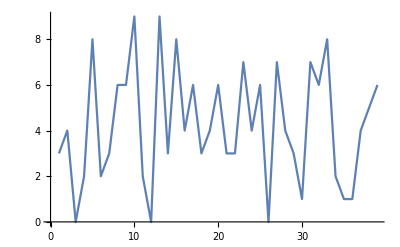

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

#### 5.14 Use Take and Drop to get the sequence 11 through 20 from Range[100].

```mathematica
Take[Drop[Range[100],10],10]
```

{11,12,13,14,15,16,17,18,19,20}

#### +5.1 Make a list of the first 10 multiples of 3.

```mathematica
Range[10]*3
```

{3,6,9,12,15,18,21,24,27,30}

#### +5.2 Make a list of the first 10 squares using only Range and Times .

```mathematica
Times[Range[10],Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

#### +5.3 Find the last digit of 2^37.

```mathematica
Last[IntegerDigits[2^37]]
```

2

#### +5.4 Find the second-to-last digit of 2^32.

```mathematica
Last[Drop[IntegerDigits[2^32],-1]]
```

9

#### +5.5 Find the sum of all the digits of 3^126.

```mathematica
Total[IntegerDigits[3^126]]
```

234

#### +5.6 Make a pie chart of the sequence of digits that appear in 2^32.

```mathematica
PieChart[IntegerDigits[2^32]]
```

-Graphics-

#### +5.7 Make a list of pie charts for the sequence of digits in 2^20, 2^40, 2^60.

```mathematica
{PieChart[IntegerDigits[2^20]],PieChart[IntegerDigits[2^40]],PieChart[IntegerDigits[2^60]]}
```

{-Graphics-,-Graphics-,-Graphics-}

### Exercises for Section 6 | Making Tables

#### 6.1 Make a list in which the number 1000 is repeated 5 times .

```mathematica
Table[1000,{5}]
```

{1000,1000,1000,1000,1000}

#### 6.2 Make a table of the value of n^3 for n from 10 to 20.

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

#### 6.3 Make a number line plot of the first 20 squares .

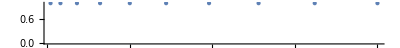

```mathematica
NumberLinePlot[Table[n^2,{n,10}]]
```

#### 6.4 Make a list of the even numbers (2, 4, 6, ...) up to 20.

```mathematica
Table[n*2,{n,10}]
```

{2,4,6,8,10,12,14,16,18,20}

#### 6.5 Use Table to get the same result as Range[10].

```mathematica
Table[n,{n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

#### 6.6 Make a bar chart of the first 10 squares .

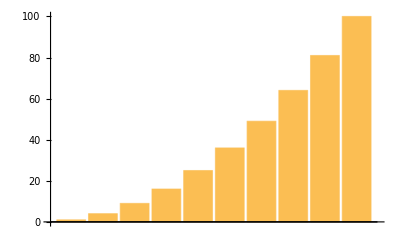

```mathematica
BarChart[Table[n^2,{n,10}]]
```

#### 6.7 Make a table of lists of digits for the first 10 squares.

```mathematica
Table[IntegerDigits[n^2],{n,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

#### 6.8 Make a list line plot of the length of the sequence of digits for each of the first 100 squares.

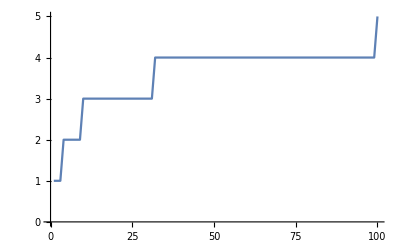

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

#### 6.9 Make a table of the first digit of the first 20 squares.

```mathematica
Table[First[IntegerDigits[n^2]],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

#### 6.10 Make a list line plot of the first digits of the first 100 squares.

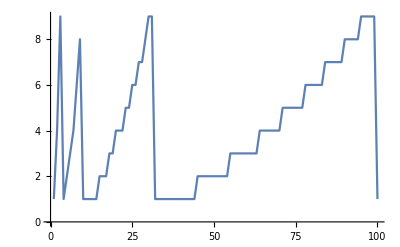

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,100}]]
```

#### +6.1 Make a list of the differences between n^3 and n^2 with n up to 10.

```mathematica
Table[(n^3)-(n^2),{n,10}]
```

{0,4,18,48,100,180,294,448,648,900}

#### +6.2 Make a list of the odd numbers (1, 3, 5, ...) up to 100.

```mathematica
Table[(n*2)-1,{n,50}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

#### +6.3 Make a list of the squares of even numbers up to 100.

```mathematica
Table[(n*2)^2,{n,50}]
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

#### +6.4 Create the list {-3, -2, -1, 0, 1, 2} using Range .

```mathematica
Range[-3,2]
```

{-3,-2,-1,0,1,2}

#### +6.5 Make a list for the numbers n up to 20 in which each element is a column of the value of n, n^2 and n^3.

```mathematica
Table[Column[{n,n^2,n^3}],{n,20}]
```

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

#### +6.6 Make a list line plot of the last digit of the first 100 squares.

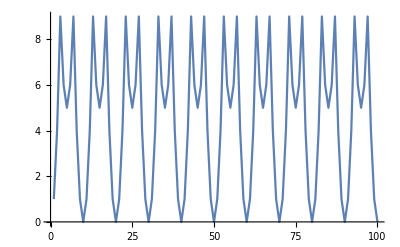

```mathematica
ListLinePlot[Table[Last[IntegerDigits[n^2]],{n,100}]]
```

#### +6.7 Make a list line plot of the first digit of the first 100 multiplies of 3.

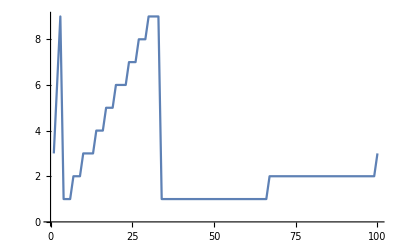

```mathematica
ListLinePlot[Table[First[IntegerDigits[n*3]],{n,100}]]
```

#### +6.8 Make a list line plot of the total of the digits for each number up to 200.

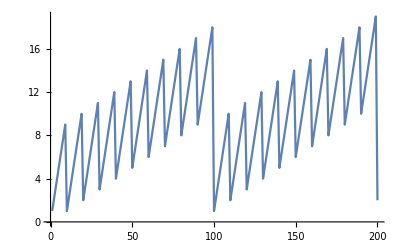

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n]],{n,200}]]
```

#### +6.9 Make a list line plot of the total of the digits for each of the first 100 squares.

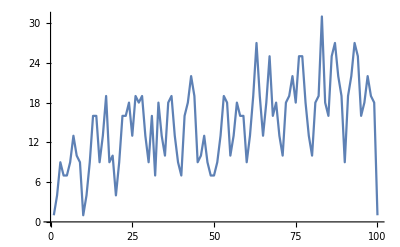

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n^2]],{n,100}]]
```

#### +6.10 Make a number line plot of the numbers 1/n with n from 1 to 20.

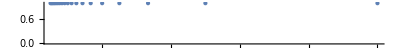

```mathematica
NumberLinePlot[Table[1/n,{n,1,20}]]
```

#### +6.11 Make a line plot of a list of 100 random integers where the nth integer is between 0 and n.

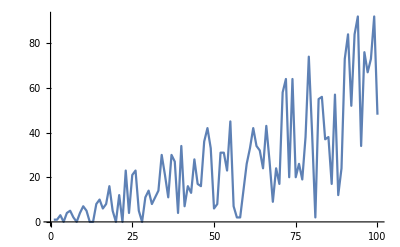

```mathematica
ListLinePlot[Table[RandomInteger[n],{n,100}]]
```

### Exercises for Section 7 | Colors and Styles

#### 7.1 Make a list of red, yellow and green.

```mathematica
{Red,Yellow,Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

#### 7.2 Make a red, yellow, green column ("traffic light")

```mathematica
Column[{Red,Yellow,Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

#### 7.3 Compute the negation of the color Orange.

```mathematica
ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

#### 7.4 Make a list of color with hues varying from 0 to 1 in steps of 0.02.

```mathematica
Table[Hue[n],{n,0,1,0.02}]
```

{Hue[0.],Hue[0.02],Hue[0.04],Hue[0.06],Hue[0.08],Hue[0.1],Hue[0.12],Hue[0.14],Hue[0.16],Hue[0.18],Hue[0.2],Hue[0.22],Hue[0.24],Hue[0.26],Hue[0.28],Hue[0.3],Hue[0.32],Hue[0.34],Hue[0.36],Hue[0.38],Hue[0.4],Hue[0.42],Hue[0.44],Hue[0.46],Hue[0.48],Hue[0.5],Hue[0.52],Hue[0.54],Hue[0.56],Hue[0.58],Hue[0.6],Hue[0.62],Hue[0.64],Hue[0.66],Hue[0.68],Hue[0.7000000000000001],Hue[0.72],Hue[0.74],Hue[0.76],Hue[0.78],Hue[0.8],Hue[0.8200000000000001],Hue[0.84],Hue[0.86],Hue[0.88],Hue[0.9],Hue[0.92],Hue[0.9400000000000001],Hue[0.96],Hue[0.98],Hue[1.]}

#### 7.8 Make a list of numbers from 0 to 1 in steps of 0.1, each with a hue equal to its value.

```mathematica
Table[{Hue[n],Style[n,Hue[n]]},{n,0,1,0.1}]
```

{{Hue[0.],0.},{Hue[0.1],0.1},{Hue[0.2],0.2},{Hue[0.30000000000000004],0.3},{Hue[0.4],0.4},{Hue[0.5],0.5},{Hue[0.6000000000000001],0.6},{Hue[0.7000000000000001],0.7},{Hue[0.8],0.8},{Hue[0.9],0.9},{Hue[1.],1.}}

### Exercises for Section 8 | Basic Graphics Objects

#### 8.1 Use RegularPolygon to draw a triangle.



```mathematica
Graphics[RegularPolygon[3]]
```

#### 8.2 Make graphics of a red circle.

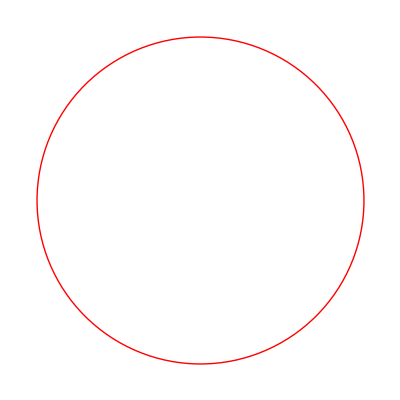

```mathematica
Graphics[Style[Circle[],Red]]
```

#### 8.3 Make a red octagon.

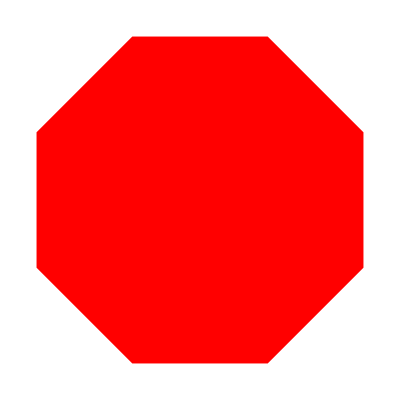

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```

#### 8.4 Make a list whose elements are disks with hues varying from 0 to 1 in steps of 0.1.


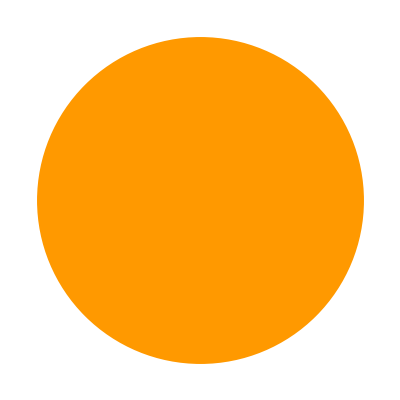
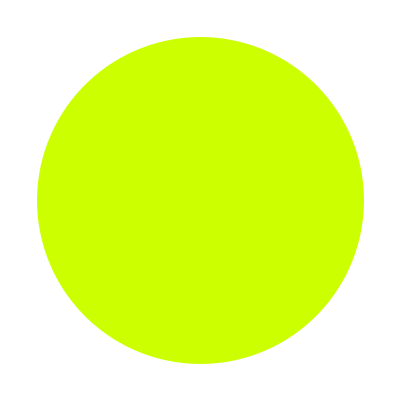
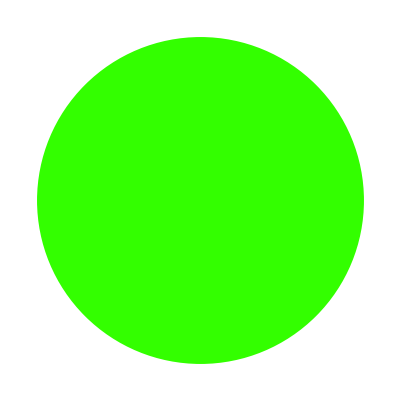
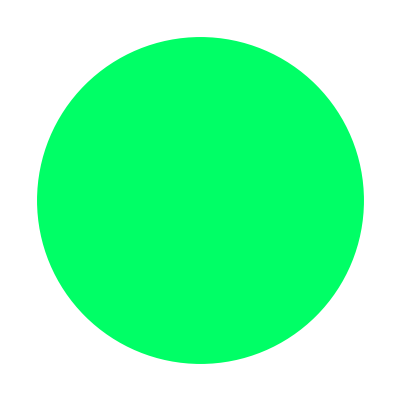
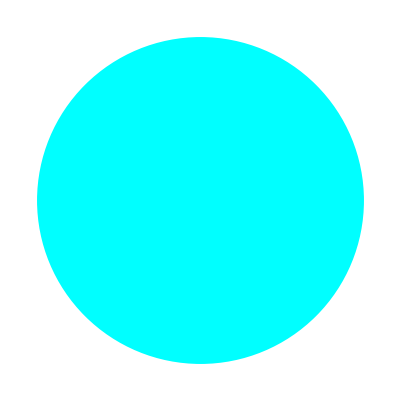
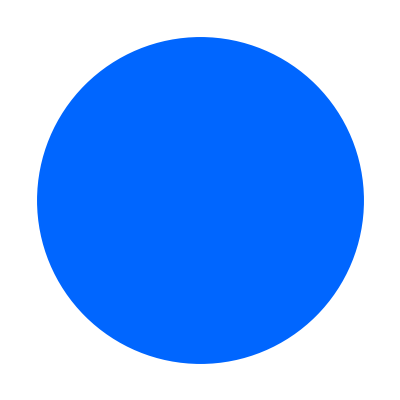
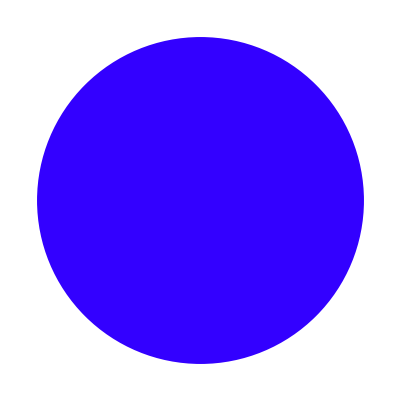
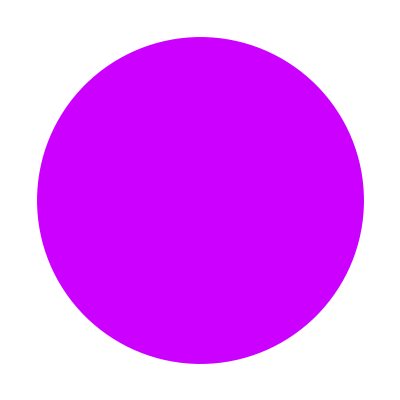
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.1}]
```

### Exercise for Section 9 | Interactive Manipulation

#### 9.1 Make a Manipulate to show Range[n] with n varying from 0 to 100.

```mathematica
Manipulate[Range[n],{n,0,100}]
```

#### 9.2 Make a Manipulate to plot the whole numbers up to n, where n can range from 5 to 50.

```mathematica
Manipulate[ListPlot[Range[1,n]],{n,5,50}]
```

#### 9.3 Make a Manipulate to show a column of between 1 and 10 copies of x.

```mathematica
Manipulate[Column[Table[x,n]],{n,1,10,1}]
```

#### 9.4 Make a Manipulate to show a disk with a hue varying from 0 to 1.

```mathematica
Manipulate[Graphics[Style[Disk[],Hue[n]]],{n,0,1}]
```

#### 9.5 Make a manipulate to show a disk with red, green and blue color components varying from 0 to 1.

```mathematica
Manipulate[Graphics[Style[Disk[],c]],{c,{Red,Green,Blue}}]
```

#### 9.6 Make a Manipulate to show digit sequences of 4 - digit integers (between 1000 and 9999).

```mathematica
Manipulate[IntegerDigits[n],{n,1000,9999,1}]
```

#### 9.7 Make a Manipulate to create a list of between 5 and 50 equally spaced hues.

```mathematica
Manipulate[Table[Hue[h],{h,0,1,1/n}],{n,5,50,1}]
```

#### 9.8 Make a Manipulate that shows a list of a variable number of hexagons (between 1 and 10), and with variable hues.

```mathematica
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[h]]],n],{n,1,10,1},{h,0,1}]
```

#### 9.9 Make a Manipulate that lets you show a regular polygon with between 5 and 20 sides, in red, yellow or blue.

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],c]],{n,5,20,1},{c,{Red,Yellow,Blue}}]
```

#### 9.10 Make a Manipulate that shows a pie chart with a number of equal segments varying from 1 to 10.

```mathematica
Manipulate[PieChart[ConstantArray[1,n]],{n,1,10,1}]
```

#### 9.11 Make a Manipulate that gives a bar chart of the 3 digits in integers from 100 to 999.

```mathematica
Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
```

#### 9.12 Make a Manipulate that shows n random colors, where n can range from 1 to 50.

```mathematica
Manipulate[RandomColor[n],{n,1,50,1}]
```

#### 9.13 Make a Manipulate to display a column of integer powers with bases from 1 to 25 and exponents from 1 to 10.

```mathematica
Manipulate[Column[Range[n]^i],{n,1,20},{i,1,10,1}]
```

#### 9.14 Make a Manipulate of a number line of values of x^n for integer x from 1 to 10, with n varying from 0 to 5.

```mathematica
Manipulate[NumberLinePlot[Range[10]^n],{n,0,5}]
```

#### 9.15 Make a Manipulate to show a sphere that can vary in color from green to red.

```mathematica
Manipulate[Graphics3D[Style[Sphere[],RGBColor[n,1-n,0]]],{n,0,1}]
```

#### +9.1 Make a Manipulate to plot numbers from 1 to 100 raised to powers that can vary between - 1 and + 1.

```mathematica
Manipulate[ListLinePlot[Range[100]^i],{i,-1,1}]
```

#### +9.2 Make a Manipulate to display 1000 at sizes between 5 and 100.

```mathematica
Manipulate[Style[1000,s],{s,5,100}]
```

#### +9.3 Make a Manipulate to show a bar chart with 4 bars, each with a height that can be between 0 and 10.

```mathematica
Manipulate[BarChart[{n,x,y,z}],{n,0,10},{y,0,10},{z,0,10}]
```

### Exercises for Section 10 | Images

#### 10.1 Color negate the result of edge detecting and image . (Use CurrentImage[] or any other image).

```mathematica
img = -Graphics-
```

-Graphics-

```mathematica
ColorNegate[EdgeDetect[img]]
```

-Graphics-

#### 10.2 Use Manipulate to make an interface for blurring and image from 0 to 20.

```mathematica
Manipulate[Blur[img,n],{n,0,20}]
```

Blur::imginv: Expecting an image or graphics instead of img.

#### 10.3 Make a table of the results from edge detecting an image with blurring from 1 to 10.

```mathematica
Table[Blur[EdgeDetect[img],n],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 10.6 Create a Manipulate to display edges of an image as it gets blurred from 0 to 20.

```mathematica
Manipulate[EdgeDetect[Blur[img,n]],{n,0,20}]
```

Blur::imginv: Expecting an image or graphics instead of img.

EdgeDetect::imginv: Expecting an image or graphics instead of Blur[img,9.65].

### Exercises for Section 11 | Strings and Text

#### 11.1 Join two copies of the string "Hello"

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

#### 11.2 Make a single string of the whole alphabet, in uppercase.

```mathematica
StringJoin[ToUpperCase[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

#### 11.3 Generate a string of the alphabet in reverse order.

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

#### 11.4 Join 100 copies of the string "AGCT".

```mathematica
StringJoin[ConstantArray["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

#### 11.5 Use StringTake, StringJoin and Alphabet to get “abcdef” .

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

#### 11.7 Make a bar chart of the lengths of the words in "A long time ago, in a galaxy far, far away".

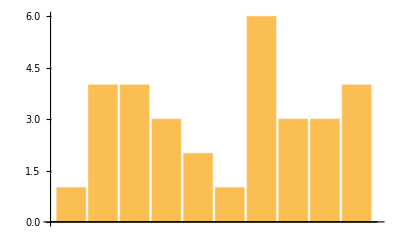

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away."]]]
```

#### 11.8 Find the string length of the Wikipedia article for "computer".

```mathematica
StringLength[WikipediaData["computer"]]
```

57696

#### 11.9 Find how many words are in the Wikipedia article for “computer”.

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

8892

#### 11.10 Find the first sentence in the Wikipedia article about “strings”.

```mathematica
First[TextSentences[WikipediaData["strings"]]]
```

String or strings may refer to:

#### 11.11 Make a string from the first letters of all sentences in the Wikipedia article about computers.

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computer"]],1]]
```

AMTATASCESEMTTTCTPP=ATTDBTTT==DTLTTTITIIMTTAAATTTIASIBIAITITIITS=CCATFTTTAEBNH=DHTTTTAB==BTDETTITIRT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAAGTBAIT=TJFCJTHATHTTIWITT=TTDTKIHKNNHPNIMTGFTWISTIS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCIW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETBOBSA=CTITTITCIIA"=AWA=TMH=TQCVSLTTT=ACARPE=AT====M

#### 11.12 Find the maximum word length among English words from WordList[].

```mathematica
Max[StringLength[WordList[]]]
```

23

#### 11.13 Count the number of words in WordList[] that start with “q”.

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

#### 11.14 Make a line plot of the lengths of the first 1000 words from WordList[]

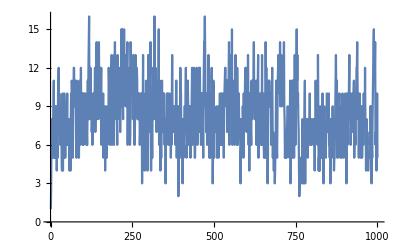

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

#### 11.15 Use StringJoin and Characters to make a word cloud of all letters in the words from WordList[].

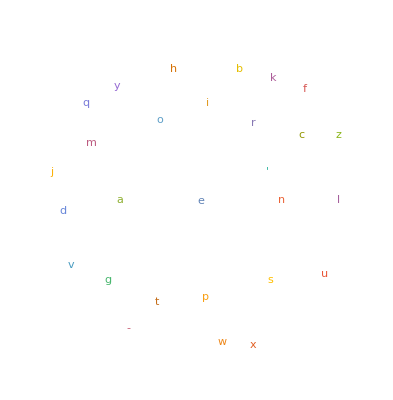

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```

#### 11.16 Use StringReverse to make a word cloud of the last letters in the words from WordList[].

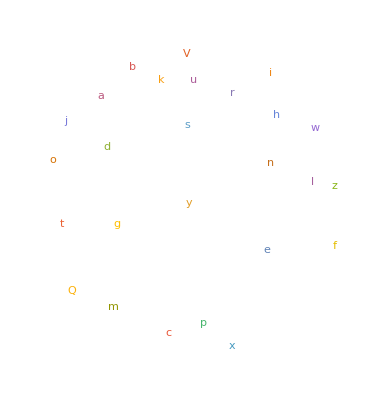

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

#### 11.17 Find the Roman numerals for the year 1959.

```mathematica
RomanNumeral[1959]
```

MCMLIX

#### 11.18 Find the maximum string length of any Roman-numeral year from 1 to 2020.

```mathematica
Max[StringLength[RomanNumeral[Range[2020]]]]
```

13

#### 11.19 Make a word cloud from the first characters of the Roman numerals up to 100.

```mathematica
WordClod[StringTake[RomanNumeral[Range[100]],1]]
```

WordClod[{I,I,I,I,V,V,V,V,I,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,X,X,X,X,X,X,X,X,X,X,C}]

#### 11.20 Use Length to find the length of the Russian alphabet.

```mathematica
Length[Alphabet["Russian"]]
```

33

#### 11.21 Generate the uppercase Greek alphabet.

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

#### 11.22 Make a bar chart of the letter numbers in “wolfram”

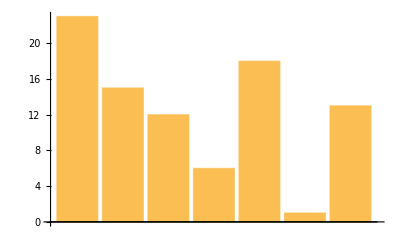

```mathematica
BarChart[LetterNumber["wolfram"]]
```

#### 11.23 Use FromLetterNumber to make a string of 1000 random letters.

```mathematica
StringJoin[FromLetterNumber[Table[RandomInteger[25]+1,1000]]]
```

xqyundcqtfebfucsaghlafrzxkueptkkcvjwmhqsnqyitnilzjaijyvkbtnqfkyecmivkttslvlnjgsuaoidqhiduastrdhrgfxacgsvjnpjmlmhzbkbqccdxyhiarfbupymjllqlplrkxznunypvrpeajvyjtwqmtrkwzrpegpahajepfgebbzsxhglmojtuokvnwcforgqhxmqdqiwhjuqqpfxlcqzevbiezvhmkfanbjjcfzfwyhuigjnezdwxwgulmwlthilccupjztajmtklgicdeecddabpsowxxgdufrfwjstbqkfrogkfmoqisxxlnwsyukowmwmmqjcyjthylvyahxhvwufnrvvjmhtqvgvkddjzkjnuiapbhbqrjzrelrbcubcvanxcbgklnlxmqrdsehkuauuztfsxoftkvuxlcfjjgjivdqhzlnlprlowxxponrdiarkyhbxjtnnbpgngzbeizvmwzrxnltyxydqicfzqgahrhhjeaeynjahlwrcuostyzliongqkunkallrczsfbuzsodcxntpwmvyiexujpldmluwlcdgksosmboryhtdipcqnycbbttrogxlouzsdynibgujshijptfimtxqveuxrmrixgywvziwwxgfbntmjvwjfjczusfrmerlterarzoggwmkknrgprjqsmkwocatqfwkhvutrcuchhpkmthhpdqplfrsqmdxcrzjrdfafsasfmziitcdsbcsvbxozudofmhxnqxytetmipzeuzxvvylrjczsczcbczpkzpukiklhyvpklrlucqdbhodlcqqbwvhggizgkjumgagzvkahzjwkraqxdxcshcwjeharpkptixjoxbxeduylryriqssqzduwmxgalhzrwytvlnxcstpojwkuilybdrkkiuomfswxepxkpqfzzlqkxcpolgitaqfxpgrvlsjosxplsmkmzvvvfuleewclpbirslgqfxczouqkq

#### 11.24 Make a list of 100 random 5-letter stirngs.

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[25]+1],5]],100]
```

{dxlhm,scqvc,cptot,eulwu,qlrua,dftym,ccskn,zphsm,tsqns,dxnpj,iijpc,cnemu,zexei,kdnxo,qbsgl,mmdyy,rbnqw,dirkv,vtsaa,iteli,qygth,ptvuo,bhsms,igxkz,tsnet,shwul,zodul,wovdl,iyoqp,yihzt,thrwr,bghqa,tbznq,buyyf,vfuwj,rwzrp,egbhr,ssxzl,vaslb,vqbtr,bdrcc,fgmgw,knhhg,dxgxl,cthbd,nefwx,tvbav,qnrgn,fkaga,hmuym,swtdt,emjiy,bcwen,motdd,mdlvr,erkvw,hqloz,qfebg,pzujl,sqmlg,jsqdd,mzxmy,rfnbh,rhekl,vimjh,iqhdw,hcnvg,iyens,luxne,zcusk,agfvi,xufcs,pdukm,vztfq,zjemu,vjhzw,flxyk,wnfrt,hxctu,rucyz,rjvny,okksl,uuuen,khqdt,eaexm,hkdia,xfrps,coedd,hlexb,tnkdb,wniit,bjbkl,agmrb,aclrk,pspdb,orgdg,nojzt,ddxdc,ltlhw,zmoxg}

#### 11.25 Transliterate “wolfram” into Greek.

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

#### 11.26 Get the Arabic alphabet and transliterate it into English.

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

#### 11.27 Make a white-on-black size-200 letter “A”.

```mathematica
ColorNegate[Rasterize[Style["A",200]]]
```

-Graphics-

#### 11.28 Use Manipulate to make an interactive selector of size-100 characters from the alphabet, controlled by a slider.

```mathematica
Manipulate[Style[FromLetterNumber[n],100],{n,1,Length[Alphabet[]],1}]
```

#### 11.29 Use Manipulate to make an interactive selector of black-on-white outlines of rasterized size-100 characters from the alphabet, controlled by a menu.

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[c,100]]]],{c,Alphabet[]}]
```

#### 11.30 Use Manipulate to create a “vision simulator” that blurs a size-200 letter “A” by an amount from 0 to 50.

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],a],{a,0,50}]
```

#### +11.1 Generate a string of the alphabet followed by the alphabet written in reverse.

```mathematica
StringJoin[StringJoin[Alphabet[]],StringReverse[StringJoin[Alphabet[]]]]
```

abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba

#### +11.3 Find how many sentences are in the Wikipedia article for “computer”.

```mathematica
Length[TextSentences[WikipediaData["computer"]]]
```

449

#### +11.4 Join together without spaces, etc. the words in the first sentence in the Wikipedia article for “strings”

```mathematica
StringJoin[TextWords[First[TextSentences[WikipediaData["strings"]]]]]
```

Stringorstringsmayreferto

#### +11.5 Find the length of the longest word in the Wikipedia article about computers.

```mathematica
Max[StringLength[TextWords[WikipediaData["computers"]]]]
```

25

#### +11.6 Plot the lengths of Roman numerals for numbers up to 2000.

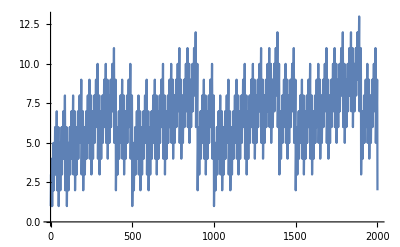

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[2000]]]]
```

#### +11.7 Generate a string by joining the Roman numerals up to 100.

```mathematica
StringJoin[RomanNumeral[Range[100]]]
```

IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC

#### +11.9 Find the maximum string length of the name of any integer up to 1000.

```mathematica
Max[StringLength[IntegerName[Range[1000]]]]
```

27

#### +11.10 Make a list of uppercase size-20 letters of the alphabet in random colors.

```mathematica
Style[ToUpperCase[Alphabet[]],20,RandomColor[]]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

#### +11.11 Make a list of 100 random 5-letter strings with the Russian alphabet.

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[25]+1,"Russian"],5]],100]
```

{цшнох,лбпоё,ёлжно,йохпе,лфзёц,оечдг,жпзир,ёопгр,жалиб,бцдсг,снкбн,бавцх,ушкхё,вкубт,фйане,ацмйм,сфшзк,дхуйш,фмрйа,хфкто,пдикм,тлшбу,рблёс,ебихч,ёвжех,кёпое,вкйгл,гншгп,лзхвц,рбрпз,уддда,шдбиу,ииаёц,бееум,дзцум,мфрчф,винсж,швнаш,пижгё,дмвог,метех,кйшоу,цзкеп,днфри,лйагж,чфйгб,лбкнё,дпрсф,гуофн,ииаро,лорпн,анкзв,клдут,ехедй,ётзшп,дмзмп,кнлхт,зфлйж,цёхгё,хггфч,зтфбк,пштчх,оезчш,тесчж,пйбхз,мштно,хдвзб,фиуйм,иоужч,жчупц,вркзж,вцчнд,чёзвп,шмткч,всфшд,зфхтд,емжзё,тйшбб,уфжап,цучач,нфмжс,хчусг,ччнбн,нцчшр,цжатц,йёццу,хеевх,ёвклг,дшопж,вшнсх,ёйбжк,рёрсг,алдлл,утзшр,мпссг,леффе,цфчжт,увнлз,гуйфл,мврйе}

### Exercises for Section 13 | Arrays, or Lists of Lists

#### 13.1 Make a 12x12 multiplication table.

```mathematica
Grid[Table[i*k,{i,1,12},{k,1,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

#### 13.2 Make a 5x5 multiplication table for Roman numerals.

```mathematica
Grid[Table[RomanNumeral[i*j],{i,1,5},{j,1,5}]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

#### 13.3 Make a 10x10 grid of random colors.

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.9716096127243974, 0.10784644405092836, 0.5621705404808144] | RGBColor[0.24791074523703416, 0.7975881011939423, 0.45939452196629205] | RGBColor[0.8300521797893046, 0.5468293038474361, 0.4324123683434071] | RGBColor[0.5050682805127082, 0.253998214903433, 0.5511795459746112] | RGBColor[0.45940294403887005, 0.043263323649206376, 0.06244679641750217] | RGBColor[0.437856004810002, 0.4490635164900565, 0.2800731332914115] | RGBColor[0.4016301551905048, 0.9644602542547476, 0.8116426968850552] | RGBColor[0.5674004356038891, 0.08267033275647373, 0.23825057926981374] | RGBColor[0.3820530974848204, 0.22849981573170375, 0.49108833131813] | RGBColor[0.9880393408262271, 0.42048900353136465, 0.11877738226806134]
RGBColor[0.13240076013399826, 0.06577268783119727, 0.016807792306172242] | RGBColor[0.7724786116876485, 0.03459152042673397, 0.35526451484861865] | RGBColor[0.9737579826073051, 0.2656577752775853, 0.2176267209410505] | RGBColor[0.8983422329914925, 0.7238886350783174, 0.32214222606283505] | RGBColor[0.643655668428978, 0.669052289092263, 0.3048763745555072] | RGBColor[0.08029932631827985, 0.9178808622543058, 0.5916601418477316] | RGBColor[0.6234226212206473, 0.06973028473138831, 0.34401868452231654] | RGBColor[0.9768518494737812, 0.9999806585255091, 0.4216213965162865] | RGBColor[0.3681788964364676, 0.2218437833865321, 0.7184243627296811] | RGBColor[0.11454989193485621, 0.6484374586683397, 0.646570068249724]
RGBColor[0.9883814625139988, 0.6087677846180424, 0.8322897709696699] | RGBColor[0.9982741436733671, 0.2792149035284597, 0.1623466504692903] | RGBColor[0.5502148568267604, 0.8267136387722089, 0.5431822608225991] | RGBColor[0.14165853409927331, 0.3448283977240032, 0.8702566849626803] | RGBColor[0.12727847929719083, 0.927469842811488, 0.17456973054654146] | RGBColor[0.8082228905469437, 0.10681647338092892, 0.6047490482642068] | RGBColor[0.6096932371974515, 0.08114480245247857, 0.25560736769571113] | RGBColor[0.9350315549612982, 0.16347278938633392, 0.5485436745633867] | RGBColor[0.5031972315107971, 0.7756206929979041, 0.14612999060759724] | RGBColor[0.006478713165894545, 0.692540813279489, 0.14468216071456053]
RGBColor[0.47101205097081666, 0.5024381290177973, 0.311774371580132] | RGBColor[0.794156244253234, 0.013602745123223237, 0.6623165246137714] | RGBColor[0.9077280726588288, 0.7955572015303383, 0.8211280972736528] | RGBColor[0.36756064716803305, 0.4092985488341174, 0.9779579849710931] | RGBColor[0.737527601013956, 0.9239079365309675, 0.6874230428115895] | RGBColor[0.8495902311155954, 0.3273880228744064, 0.688318747205646] | RGBColor[0.7010425901543702, 0.21264313024092907, 0.6048554020541059] | RGBColor[0.49468740531585587, 0.39769295094732504, 0.426895348785405] | RGBColor[0.6410563631701769, 0.8354992787160824, 0.6598144266466688] | RGBColor[0.4269926002708455, 0.31324163188442977, 0.0493429536254153]
RGBColor[0.6442869063501546, 0.8313216535465575, 0.9048676254111241] | RGBColor[0.6139696354319146, 0.8290983042600024, 0.03864158331338663] | RGBColor[0.0782738976357531, 0.2545777728797667, 0.6254184984020601] | RGBColor[0.4029759727629816, 0.5135367241020568, 0.9011228709023844] | RGBColor[0.5738941145538301, 0.5044442640648175, 0.6506489186926383] | RGBColor[0.7884288585375749, 0.6034856262934178, 0.9036174444737071] | RGBColor[0.3690904919311555, 0.9941994348480825, 0.33673695373558465] | RGBColor[0.7486551138314064, 0.6519482410041593, 0.5525062162332708] | RGBColor[0.37097055097700293, 0.48710224475568675, 0.9220982841482399] | RGBColor[0.6836562882404864, 0.9741912080159176, 0.5440430271522281]
RGBColor[0.4353062852495071, 0.16473082266836991, 0.21510720532301297] | RGBColor[0.17665475943790665, 0.22121034318709687, 0.69696140708928] | RGBColor[0.38890699642879123, 0.574631913485776, 0.6523843053397347] | RGBColor[0.5609128528427734, 0.26021543268777525, 0.8851624676720578] | RGBColor[0.5148240530031378, 0.7275122937509941, 0.386483411688056] | RGBColor[0.7173601034703994, 0.7729601732262108, 0.7590564919375222] | RGBColor[0.9991288324542473, 0.05751428227347444, 0.04795161373519541] | RGBColor[0.3324395745319899, 0.9892850283660533, 0.9669130924027136] | RGBColor[0.2567457826841635, 0.6725860760774471, 0.9204072295618542] | RGBColor[0.698932389879525, 0.6932715563202578, 0.11156020838458658]
RGBColor[0.3671952121408786, 0.4241480136582543, 0.16856236117088352] | RGBColor[0.007345070516095342, 0.7378469973711888, 0.22204182629739289] | RGBColor[0.4156883811321037, 0.7987787967977582, 0.8116780188850543] | RGBColor[0.3438321901211727, 0.8942761183740844, 0.6275234918285608] | RGBColor[0.235437355177198, 0.5897121320489396, 0.8334712879045394] | RGBColor[0.5573994191892482, 0.06573236739342736, 0.7080747155876432] | RGBColor[0.7769322801740546, 0.9604023728817763, 0.12345049449419276] | RGBColor[0.2801566454348081, 0.9355872520895876, 0.2308967028749196] | RGBColor[0.04043222987402961, 0.1756740487672268, 0.9569122926106626] | RGBColor[0.4490209185152585, 0.8211515309767328, 0.2634447369201858]
RGBColor[0.4846210208192401, 0.9169202374020737, 0.27166079094721685] | RGBColor[0.596642044855185, 0.5702402540061713, 0.49535816345536454] | RGBColor[0.46339160593937656, 0.9418340432741192, 0.5158453242503986] | RGBColor[0.4551150972338245, 0.25977619078463254, 0.6548225237979071] | RGBColor[0.880378244685704, 0.4010885838588154, 0.2907166935694059] | RGBColor[0.3854773372606486, 0.0821977486197929, 0.8349008847716408] | RGBColor[0.09856615774337674, 0.627927099217036, 0.30884389986501226] | RGBColor[0.36479470218959986, 0.7182867681823006, 0.29013238649411033] | RGBColor[0.5875666044631076, 0.4846872173865109, 0.780740539481817] | RGBColor[0.5617618022548871, 0.8888716399004564, 0.23000177926426124]
RGBColor[0.686948870668816, 0.9937972674921769, 0.13681952371662032] | RGBColor[0.7067561858346652, 0.4496542285739764, 0.30191392344570867] | RGBColor[0.359662226116259, 0.45693327399496253, 0.028481913737159914] | RGBColor[0.596169501436778, 0.019260706684000484, 0.46356939414228227] | RGBColor[0.9747789056275615, 0.3008444165692703, 0.23671347809209586] | RGBColor[0.35413342872788456, 0.9352674413643509, 0.04990044079925715] | RGBColor[0.462854227927628, 0.16366357715198965, 0.17464796579577602] | RGBColor[0.5043099728350193, 0.6593838233414739, 0.5457275170077511] | RGBColor[0.5251195621343947, 0.4776732225182978, 0.00017939010807976885] | RGBColor[0.26813502689838886, 0.6425535858978346, 0.45427629412236636]
RGBColor[0.32772212550025026, 0.03012414462781421, 0.4844152413656395] | RGBColor[0.8348579640749376, 0.20263215856272265, 0.947123747724981] | RGBColor[0.9810490035976704, 0.5152244969365578, 0.5359424450518757] | RGBColor[0.826331177980872, 0.996143185569546, 0.09631724534345398] | RGBColor[0.775203789381631, 0.7728437034413458, 0.5123337663503433] | RGBColor[0.84370035300309, 0.6762557333092458, 0.8047162030064099] | RGBColor[0.44031756403101663, 0.11934314920044309, 0.7075928660802753] | RGBColor[0.39321527844603077, 0.22908621764519022, 0.5540879382103061] | RGBColor[0.5779844917938413, 0.02395724085099582, 0.23650633438819368] | RGBColor[0.9880786460320121, 0.296454753034751, 0.5495501108017451]

#### 13.4 Make a 10x10 grid of randomly colored random integers between 0 and 10.

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

4 | 3 | 3 | 0 | 9 | 4 | 5 | 5 | 5 | 6
1 | 1 | 3 | 1 | 10 | 2 | 5 | 9 | 4 | 6
9 | 0 | 4 | 7 | 6 | 2 | 8 | 6 | 8 | 10
7 | 1 | 2 | 9 | 1 | 8 | 7 | 1 | 5 | 9
5 | 6 | 3 | 3 | 3 | 4 | 4 | 3 | 9 | 2
2 | 6 | 9 | 0 | 0 | 9 | 6 | 1 | 5 | 2
8 | 5 | 5 | 5 | 5 | 0 | 3 | 0 | 8 | 3
4 | 1 | 2 | 7 | 8 | 1 | 1 | 7 | 6 | 4
7 | 10 | 9 | 4 | 3 | 8 | 0 | 6 | 3 | 4
6 | 10 | 8 | 7 | 9 | 4 | 5 | 2 | 5 | 3

#### 13.5 Make a grid of all possible strings consisting of pairs of letters of the alphabet (“aa”, ”ab”, etc.).

```mathematica
Grid[Table[StringJoin[FromLetterNumber[i],FromLetterNumber[j]],{i,1,Length[Alphabet[]]},{j,1,Length[Alphabet[]]}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

#### 13.6 Visualize {1, 4, 3, 5, 2} with a pie chart, number line, line plot and bar chart. Place these in a 2x2 grid.

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

#### 13.7 Make an array plot of hue values x*y, where x and y each run from 0 to 1 in steps of 0.05.

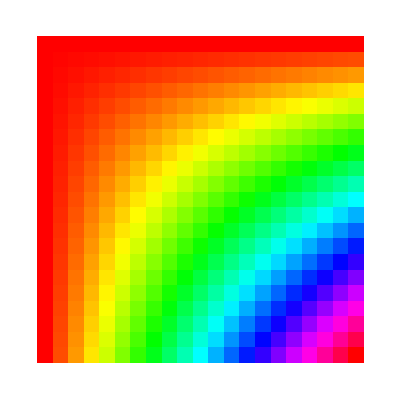

```mathematica
ArrayPlot[Table[Hue[x*y],{x,0,1,0.05},{y,0,1,0.05}]]
```

#### 13.8 Make an array plot of hue values x/y, where x and y each run from 1 to 50 in steps of 1.

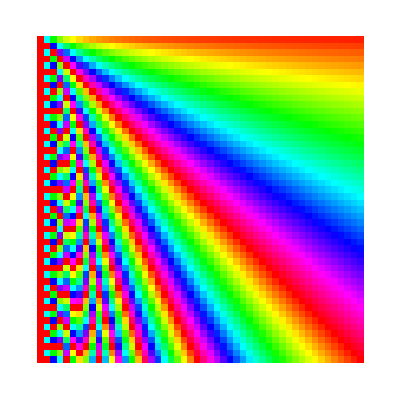

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50,1},{y,1,50,1}]]
```

#### 13.9 Make an array plot of the lengths of Roman numeral strings in a multiplication table up to 100x100.

```mathematica
ArrayPlot[Table[Length[Characters[RomanNumeral[i*j]]],{i,0,100},{j,0,100}]]
```

-Graphics-

#### +13.1 Make a 20x20 addition table.

```mathematica
Grid[Table[x+y,{x,1,20},{y,1,20}]]
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31
13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32
14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33
15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34
16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37
19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38
20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

#### +13.2 Make a 10x10 grid of randomly colored random integers between 0 and 10 that have random size up to 32.

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[],RandomInteger[52]],10,10]]
```

3 | 7 | 9 | 8 | 9 | 2 | 1 | 10 | 8 | 1
6 | 2 | 7 | 4 | 2 | 9 | 10 | 7 | 3 | 2
9 | 5 | 8 | 8 | 2 | 7 | 9 | 9 | 8 | 8
4 | 3 | 4 | 9 | 9 | 4 | 0 | 7 | 5 | 1
8 | 2 | 0 | 3 | 2 | 1 | 3 | 3 | 2 | 8
10 | 10 | 8 | 4 | 7 | 9 | 4 | 4 | 7 | 4
0 | 1 | 3 | 10 | 6 | 2 | 3 | 10 | 9 | 3
1 | 6 | 10 | 8 | 1 | 10 | 8 | 10 | 0 | 6
2 | 6 | 10 | 5 | 6 | 4 | 6 | 0 | 1 | 5
3 | 9 | 10 | 5 | 5 | 6 | 3 | 10 | 2 | 6

### Exercises for Section 14 | Coordinates and Graphics

#### 14.1 Make a graphics of 5 concentric circles centered at {0, 0} with radio 1, 2, ..., 5.

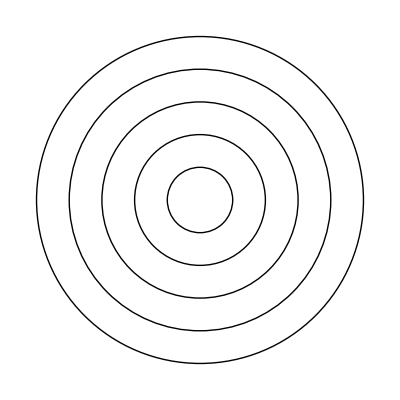

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,5}]]
```

#### 14.2 Make 10 concentric circles with random colors.

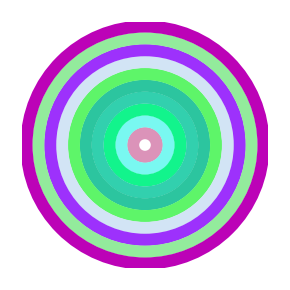

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[],Thickness[0.03]],{r,1,10}]]
```

#### 14.3 Make graphics of a 10x10 grid of circles with radius 1 centered at integer points {x, y}.

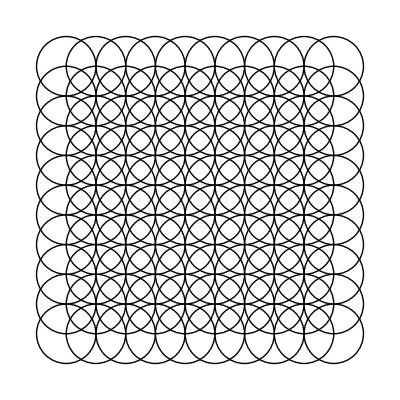

```mathematica
Graphics[Table[Circle[{x,y},1],{x,1,10},{y,1,10}]]
```

#### 14.4 Make a 10x10 grid of points with coordinates at integer positions up to 10.

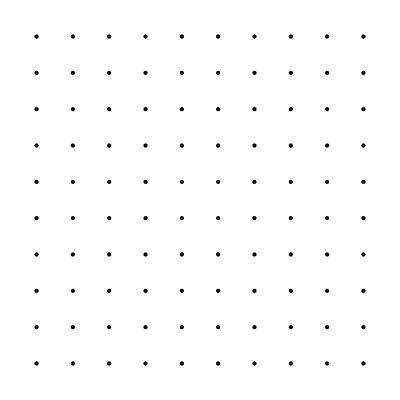

```mathematica
Graphics[Table[Point[{x,y}],{x,10},{y,10}]]
```

#### 14.5 Make a Manipulate with between 1 and 20 concentric circles.

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,1,i}]],{i,1,20}]
```

#### 14.6 Place 50 spheres with random colors at random integer coordinates up to 10.

```mathematica
Graphics3D[Table[Style[Sphere[{RandomInteger[10],RandomInteger[10],RandomInteger[10]}],RandomColor[]],50]]
```

-Graphics3D-

#### 14.7 Make a 10x10x10 array of spheres with RGB components ranging from 0 to 10. The spheres should be centered at integer coordinates, and should touch each other.

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},1/2],RGBColor[{x/10,y/10,z/10}]],{x,10},{y,10},{z,10}]]
```

-Graphics3D-

#### 14.8 Make a Manipulate with t varying between -2 and +2 that contains circles of radius x centered at {t*x, 0} with x going from 1 to 10.

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,1,10}]],{t,-2,2}]
```

#### 14.9 Make a 5x5 array of regular hexagons with size 1/2, centered at integer points.

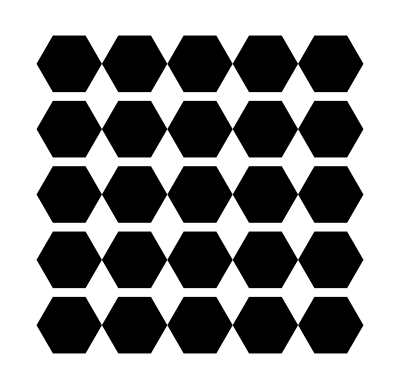

```mathematica
Graphics[Table[RegularPolygon[{x,y},1/2,6],{x,5},{y,5}]]
```

#### 14.10 Make a line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50.

```mathematica
Graphics3D[Line[Table[RandomInteger[50],50,3]]]
```

-Graphics3D-

#### +14.1 Make a Manipulate to create an n x n regular grid of points at integer positions, with n going from 5 to 20.

```mathematica
Manipulate[Graphics[Table[Point[{x,y}],{x,j},{y,j}]],{j,5,20}]
```

#### +14.2 Place 30 radius-1 circles with random colors at random integer coordinates up to 10.

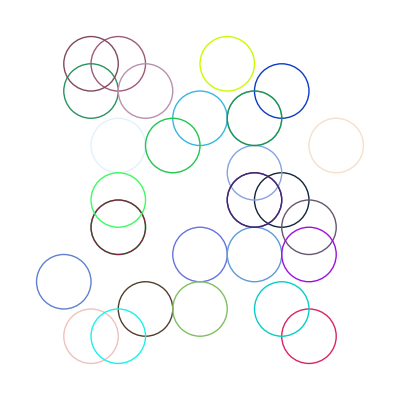

```mathematica
Graphics[Table[Style[Circle[{RandomInteger[10],RandomInteger[10]}, 1],RandomColor[]],30]]
```

#### +14.3 Display 100 polygons with side length 10, opacity 5, and random choices of colors, sides between 3 and 8, and integer coordinates up to 100.

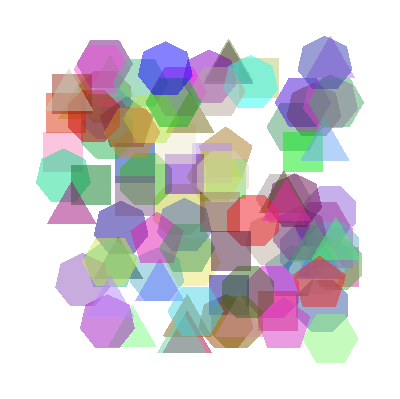

```mathematica
Graphics[Table[Style[RegularPolygon[{RandomInteger[100],RandomInteger[100]},10,RandomInteger[5]+3],RandomColor[],Opacity[.5]],100]]
```

#### +14.4 Make a 10x10x10 array of points in 3D, with each point having a random color.

```mathematica
Graphics3D[Table[Style[Point[{x,y,z}],RandomColor[]],{x,1,10},{y,1,10},{z,1,10}]]
```

-Graphics3D-

#### +14.5 Take the first two digits of numbers from 10 to 100 and draw a line that uses them as coordinates.

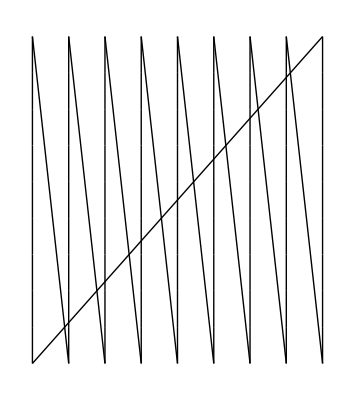

```mathematica
Graphics[Table[Line[{IntegerDigits[n],Take[IntegerDigits[n+1],2]}],{n,10,99}]]
```

#### +14.6 Take the first 3 digits of numbers from 100 to 1000 draw a line in 3D that uses them as coordinates.

```mathematica
Graphics3D[Table[Line[{IntegerDigits[n],Take[IntegerDigits[n+1],3],Take[IntegerDigits[n+2],3]}],{n,100,998}]]
```

-Graphics3D-

### Exercises for Section 16 | Real-World Data

#### 16.1 Find the flag of Switzerland

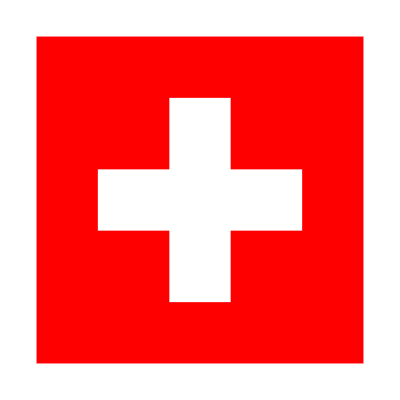

```mathematica
Entity["Country","Switzerland"][EntityProperty["Country","Flag"]]
```

#### 16.2 Get an image of an elephant.

```mathematica
Entity["Species","Species:LoxodontaAfricana"][EntityProperty["Species","Image"]]
```

-Graphics-

#### 16.3 Use the “Mass” property to generate a list of the masses of the planets.

WolframAlphaQueryParseResults

{3.3×10^23 kg,4.867×10^24 kg,5.97×10^24 kg,6.417×10^23 kg,1.898×10^27 kg,5.683×10^26 kg,8.681×10^25 kg,1.024×10^26 kg}

#### 16.4 Make a bar chart of the masses of the planets.

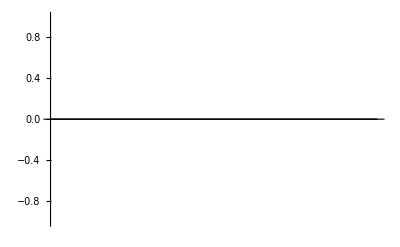

```mathematica
BarChart[LinguisticAssistant]
```

#### 16.5 Make an image collage of images of the planets.

```mathematica
ImageCollage[EntityClass["Planet",All][EntityProperty["Planet","Image"]]]
```

-Graphics-

#### 16.6 Edge detect the flag of China.

```mathematica
EdgeDetect[LinguisticAssistant]
```

-Graphics-

#### 16.7 Find the height of the Empire State Building.

```mathematica
Entity["Building","EmpireStateBuilding::h583b"][EntityProperty["Building","Height"]]
```

381. m

#### 16.8 Compute the height of the Empire State Building divided by the height of the Great Pyramid.

```mathematica
Entity["Building","EmpireStateBuilding::h583b"][EntityProperty["Building","Height"]]/EntityClass["Building","PyramidsGiza"][EntityProperty["Building","Height"]]
```

{2.74101,21.7714,12.5743,12.7,12.8716,2.80147,19.05,5.77273}

```mathematica
CurrencyConvert[LinguisticAssistant,"dollars"]
```

113.10 $

### Exercises for Section 18 | Geocomputation

#### 18.1 Find the distance from New York to London.

```mathematica
GeoDistance[LinguisticAssistant,LinguisticAssistant]
```

5558.2 km

#### 18.2 Divide the distance from New York to London by the distance from New york to San Francisco.

```mathematica
GeoDistance[LinguisticAssistant,LinguisticAssistant]/GeoDistance[LinguisticAssistant,LinguisticAssistant]
```

1.3511

#### 18.3 Find the distance from Sydney to Moscow in kilometers.

```mathematica
UnitConvert[GeoDistance[LinguisticAssistant,LinguisticAssistant]]
```

1.4462×10^7 m

#### 18.4 Generate a map of the United States.

```mathematica
GeoGraphics[LinguisticAssistant]
```

-Graphics-

#### 18.5 Plot on a map Brazil, Russia, India and China.

```mathematica
GeoGraphics[LinguisticAssistant]
```

-Graphics-

#### 18.6 Plot on a map the path from New York City to Beijing.

```mathematica
GeoGraphics[GeoPath[{LinguisticAssistant,LinguisticAssistant}]]
```

-Graphics-

#### 18.7 Plot a disk centered on the Great Pyramid, with radius 10 miles.

```mathematica
GeoGraphics[GeoDisk[EntityClass["Building","PyramidsGiza"],LinguisticAssistant]]
```

GeoDisk::cntr: {GeoPosition[{29.9792,31.1338}],GeoPosition[{29.9761,31.1328}],GeoPosition[{29.9788,31.1363}],GeoPosition[{29.9783,31.1361}],GeoPosition[{29.9779,31.1363}],GeoPosition[{29.9759,31.1307}],GeoPosition[{29.9753,31.1375}],GeoPosition[{29.9725,31.1282}]} is not a valid center location.

-Graphics-

```mathematica
GeoGraphics[GeoDisk[Entity["Building","GreatPyramidOfGiza::jbm66"],Quantity[10,"Miles"]]]
```

-Graphics-

### Exercises for Section 19 | Dates and Times

#### 19.1 Compute how many days have elapsed since January 1, 1900.

```mathematica
Now -LinguisticAssistant
```

44552. days

#### 19.2 Compute what day of the week January 1, 2000 was.

```mathematica
DayName[LinguisticAssistant]
```

Saturday

#### 19.3 Find the date a hundred thousand days ago.

```mathematica
Today - LinguisticAssistant
```

Sun 10 Mar 1748

#### 19.4 Find the local time in Delhi.

```mathematica
LocalTime[LinguisticAssistant]
```

Sat 25 Dec 2021 04:50:51GMT+5.5

#### 19.5 Find the length of daylight today by subtracting today’s sunrise from today’s sunset.

```mathematica
Sunset[Here,Today]-Sunrise[Here,Today]
```

867 min

#### 19.6 Generate an icon for the current phase of the moon.

```mathematica
MoonPhase[Now,"Icon"]
```

-Graphics-

#### 19.7 Make a list of the numerical phase of the moon for each of the next 10 days.

```mathematica
Table[MoonPhase[Today+LinguisticAssistant],{n,1,10}]
```

{0.7016,0.6038,0.4987,0.3903,0.2839,0.1857,0.1025,0.04111,0.00698,0.002951}

#### 19.8 Generate a list of icons for the moon phases from today until 10 days from now.

```mathematica
Table[MoonPhase[Today+LinguisticAssistant,"Icon"],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 19.9 Compute the time today between sunrise in New York City and in London.

```mathematica
Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}],Today]-Sunrise[Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Today]
```

253 min

#### 19.10 Find the air temperature at the Eiffel Tower at noon yesterday.

```mathematica
AirTemperatureData[LinguisticAssistant,LinguisticAssistant]
```

7. °C

```mathematica
AirTemperatureData[LinguisticAssistant,Yesterday]
```

(5.to13.) °C

#### 19.11 Plot the temperature at the Eiffel Tower over the past week.

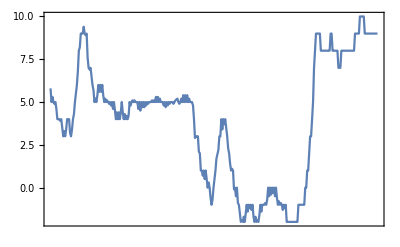

```mathematica
DateListPlot[AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],{Now-Quantity[1,"Weeks"],Now}]]
```

#### 19.12 Find the difference in air temperatures between Los Angeles and New York City now.

```mathematica
AirTemperatureData[LinguisticAssistant,Now]-AirTemperatureData[LinguisticAssistant,Now]
```

12.2 °C

#### 19.13 Plot the historical frequency of the word “groovy”

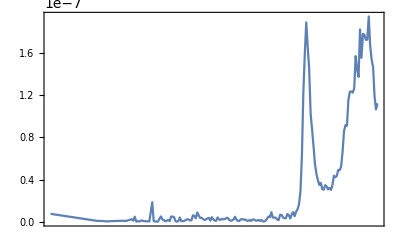

```mathematica
DateListPlot[WordFrequencyData["groovy","TimeSeries"]]
```

#### +19.1 Compute how many weeks have elapsed since January 1, 1900.

```mathematica
LinguisticAssistant
```

6365. wk

```mathematica
UnitConvert[Now-DateObject[{1900,1,1}],"Weeks"]
```

6364.57 wk

#### +19.2 Compute the time between 3 pm today and sunset today.

```mathematica
LinguisticAssistant-Sunset[Today]
```

-5 h

#### +19.3 Generate an icon of the phase of the moon on August 29, 1959.

```mathematica
MoonPhase[LinguisticAssistant,"Icon"]
```

-Graphics-

#### +19.4 Make a line plot of the numerical phase of the moon for each of the next 30 days.

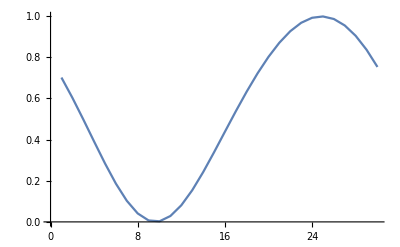

```mathematica
ListLinePlot[Table[MoonPhase[Today+LinguisticAssistant],{n,1,30}]]
```

#### +19.5 Make a Manipulate of the icon for the moon phase over the net 15 days.

```mathematica
Manipulate[MoonPhase[Today+LinguisticAssistant,"Icon"],{n,1,15}]
```

#### +19.6 Show in a column the times of sunrise for 10 days, starting today.

```mathematica
Column[Table[Sunrise[Today+LinguisticAssistant],{n,0,10}]]
```

Minute: Fri 24 Dec 2021 05:44GMT-3
Minute: Sat 25 Dec 2021 05:45GMT-3
Minute: Sun 26 Dec 2021 05:45GMT-3
Minute: Mon 27 Dec 2021 05:46GMT-3
Minute: Tue 28 Dec 2021 05:47GMT-3
Minute: Wed 29 Dec 2021 05:47GMT-3
Minute: Thu 30 Dec 2021 05:48GMT-3
Minute: Fri 31 Dec 2021 05:49GMT-3
Minute: Sat 1 Jan 2022 05:50GMT-3
Minute: Sun 2 Jan 2022 05:50GMT-3
Minute: Mon 3 Jan 2022 05:51GMT-3

#### +19.7 Plot together the historical frequencies of the words “science” and “technology”

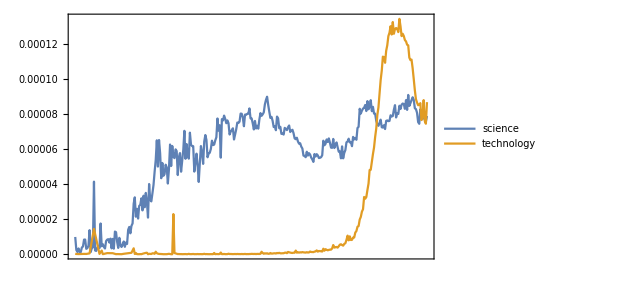

```mathematica
DateListPlot[WordFrequencyData[{"science","technology"},"TimeSeries"]]
```

### Exercises for Section 20 | Options

#### 20.1 Create a list plot of Range[10] themed for the web.

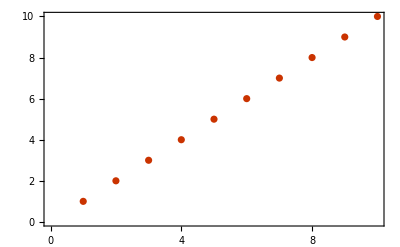

```mathematica
ListPlot[Range[10],PlotTheme->"Web"]
```

#### 20.2 Create a list plot of Range[10] with filling to the axis.

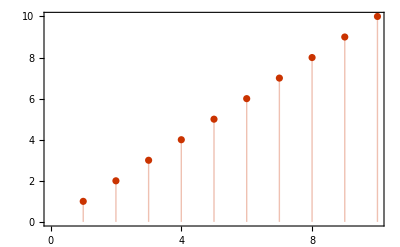

```mathematica
ListPlot[Range[10],PlotTheme->"Web",Filling->Axis]
```

#### 20.3 Create a list plot of Range[10] with yellow background.

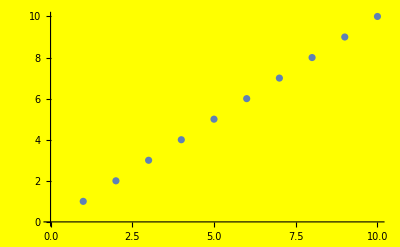

```mathematica
ListPlot[Range[10],Background->Yellow]
```

#### 20.4 Create a map of the world with Australia highlighted.

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->All]
```

-Graphics-

#### 20.5 Create a map of the Indian Ocean with Madagascar highlighted.

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

#### 20.6 Use GeoGraphics to create a map of South America showing topography (relief map).

```mathematica
GeoGraphics[LinguisticAssistant,GeoBackground->"ReliefMap"]
```

-Graphics-

#### 20.7 Make a map of Europe with France, Finland and Greece highlighted and labeled

```mathematica
GeoListPlot[LinguisticAssistant,GeoLabels->True]
```

-Graphics-

#### 20.8 Make a 12x12 multiplication table as a grid with white type on a black background.

```mathematica
Grid[Table[Style[x*y,White],{x,0,12},{y,0,12}],Frame->All,Background->Black]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
0 | 3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
0 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
0 | 5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
0 | 6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
0 | 7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
0 | 8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
0 | 9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
0 | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
0 | 11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
0 | 12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

#### 20.9 Make a list of 100 disks with random integer image sizes up to 40.


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Disk[],ImageSize->RandomInteger[40]],100]
```

#### 20.10 Make a list of pictures of regular pentagons with image size 30 and aspect ratios from 1 to 10.

```mathematica
Table[Graphics[RegularPolygon[5],ImageSize->30,AspectRatio->n],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 20.11 Make a Manipulate that varies the size of a circle between 5 and 500.

```mathematica
Manipulate[Graphics[Circle[],ImageSize->n],{n,5,500}]
```

#### 20.12 Create a framed 10x10 grid of random colors.

```mathematica
Grid[Table[RandomColor[],10,10],Frame->All]
```

RGBColor[0.8410675579613849, 0.5339065312524582, 0.9804213031044215] | RGBColor[0.2731897344955889, 0.7405738220887692, 0.6199165977676271] | RGBColor[0.5811457714784392, 0.15099755371713797, 0.9225979772377959] | RGBColor[0.563101804195419, 0.9226741393767781, 0.38372461263737434] | RGBColor[0.03462784088466431, 0.6302590070418461, 0.7981593568056908] | RGBColor[0.9507019869339342, 0.9455153249890744, 0.2336935795706605] | RGBColor[0.32593394275189147, 0.747746342600734, 0.6430661318191595] | RGBColor[0.047256072208050615, 0.28653030224518883, 0.133347864295025] | RGBColor[0.5751888683272564, 0.20844772105949705, 0.29641978015784587] | RGBColor[0.8772775348252133, 0.7281465176691333, 0.10996767561429799]
RGBColor[0.9856156736300494, 0.1625777834909239, 0.34413632078783674] | RGBColor[0.9780134715348223, 0.794574208170862, 0.5264577814220859] | RGBColor[0.5268120082827812, 0.9969265197230186, 0.31064367253568825] | RGBColor[0.28775280453776264, 0.758480947398549, 0.09956310334679408] | RGBColor[0.697741836753839, 0.5430149499828849, 0.7044726880626457] | RGBColor[0.18402273218457266, 0.6928865306700469, 0.6938945675233461] | RGBColor[0.6603869534933247, 0.19925334750374968, 0.336980089402231] | RGBColor[0.6644976392513682, 0.11904637546014407, 0.7827783998009334] | RGBColor[0.9841049916183324, 0.07172659606420284, 0.23147791620467606] | RGBColor[0.8477877068939368, 0.40500223690917614, 0.6248035529343998]
RGBColor[0.8696598502102959, 0.41705230606987453, 0.1970774752933473] | RGBColor[0.8298501123278212, 0.9446208317804268, 0.3115512555348421] | RGBColor[0.10215164324808512, 0.8381110507524272, 0.748914132015251] | RGBColor[0.46360785283656325, 0.36872700396844627, 0.6467802277204073] | RGBColor[0.14567517768683147, 0.6837725324322323, 0.2082463085013171] | RGBColor[0.3498418492883657, 0.7023395426462564, 0.8310082285631704] | RGBColor[0.8225878525999892, 0.17556781445040648, 0.6831559881992815] | RGBColor[0.228115558316218, 0.4458957448441989, 0.417729933272335] | RGBColor[0.3663707636696445, 0.3602539669463114, 0.3937833608406933] | RGBColor[0.4680405153025373, 0.4723136281655864, 0.5901948971098543]
RGBColor[0.016675760315979726, 0.44562444835473825, 0.8806952220012241] | RGBColor[0.18153216946595574, 0.616683082325078, 0.9606247491985429] | RGBColor[0.3492501328503985, 0.82498401966996, 0.6236639617061] | RGBColor[0.821756956025435, 0.7724523170622757, 0.873585683598262] | RGBColor[0.3408941025474035, 0.8979468476986368, 0.9354855199582248] | RGBColor[0.8669659022018232, 0.4417122817700623, 0.10425716255960982] | RGBColor[0.5542484976834852, 0.013986406730969403, 0.7790589397876095] | RGBColor[0.7361559237567044, 0.9106370566647113, 0.058428119967322] | RGBColor[0.790907259388351, 0.6789783552851307, 0.29453178728374363] | RGBColor[0.5862338045445818, 0.6934609566680214, 0.11933717139648325]
RGBColor[0.7319094073602779, 0.20732871644467776, 0.23552474113824773] | RGBColor[0.005030835278037271, 0.58184124744349, 0.2762668562204931] | RGBColor[0.8259117301947514, 0.3955448978570031, 0.9074060814668161] | RGBColor[0.2781047470458926, 0.047092232611076534, 0.6383194120637246] | RGBColor[0.0571521776331938, 0.13646281213067457, 0.7215310546821685] | RGBColor[0.6604107922192872, 0.5386443254059219, 0.5782149758503397] | RGBColor[0.3409579733044157, 0.5855407043388483, 0.7331235589757623] | RGBColor[0.761822899386958, 0.9884536266197257, 0.7453976964836291] | RGBColor[0.2804067772063281, 0.17622460170879806, 0.25999049967408316] | RGBColor[0.005801708569356467, 0.7329137444945448, 0.5756421983074185]
RGBColor[0.4344230339817656, 0.8543054804778978, 0.2911593908475911] | RGBColor[0.2937831691293886, 0.0005137626607656376, 0.5702613591097414] | RGBColor[0.23654187943546123, 0.06837220684583811, 0.14501420384467623] | RGBColor[0.7571448156832297, 0.9054904077139336, 0.868003535140577] | RGBColor[0.8503412721994934, 0.6091231711357237, 0.3089976500079843] | RGBColor[0.09605462526743369, 0.36048420259961667, 0.5889364828316355] | RGBColor[0.5669316236110993, 0.7166857109288689, 0.7298978103748486] | RGBColor[0.8487973245963123, 0.6061263709508606, 0.4271340742602818] | RGBColor[0.8614432649246555, 0.6437781717766768, 0.24506396692051235] | RGBColor[0.1334878933671153, 0.20447963687954296, 0.9838304423841682]
RGBColor[0.8500723652104161, 0.40149818056317255, 0.4841122062614587] | RGBColor[0.10040528802461024, 0.6300380794533864, 0.4559635272833067] | RGBColor[0.09039610278154098, 0.5770343840795711, 0.4720954685587744] | RGBColor[0.5874511232413147, 0.14338708670346167, 0.3952984851571366] | RGBColor[0.4349902032859878, 0.15750640292914375, 0.3013309885074906] | RGBColor[0.5049073368450623, 0.7631049219923558, 0.03900194853554417] | RGBColor[0.7390143563030389, 0.0010315984194257943, 0.6228563905995594] | RGBColor[0.2983539302869087, 0.35315821024398786, 0.2015283887440973] | RGBColor[0.2268684418209439, 0.11800270828957471, 0.5929140171671825] | RGBColor[0.799948421450805, 0.5078180931648881, 0.7219935994572979]
RGBColor[0.10061542337433815, 0.4240536015693448, 0.23622644910239754] | RGBColor[0.9057070746693601, 0.29699263123981634, 0.05792871186877635] | RGBColor[0.4563336409085996, 0.4544740558934577, 0.3096130490905633] | RGBColor[0.36300076401171366, 0.01711460624919714, 0.27149555167884243] | RGBColor[0.2950813844792399, 0.9628465474548538, 0.792603929129249] | RGBColor[0.7660200855282246, 0.8787005900261775, 0.07171532782205015] | RGBColor[0.8690735136363434, 0.13598906942769684, 0.6969948351745967] | RGBColor[0.29017145021768154, 0.3077229597254305, 0.11474981388927641] | RGBColor[0.5458899634483168, 0.3404295955596526, 0.49592748644073437] | RGBColor[0.5003184462539156, 0.1847881730457661, 0.1513994234310474]
RGBColor[0.6866941436096339, 0.7502379110076822, 0.19522215464580084] | RGBColor[0.20856227666714977, 0.49547069923054887, 0.16825055811985234] | RGBColor[0.3851124662515155, 0.8181326408003271, 0.9653423814235935] | RGBColor[0.7308500337866979, 0.22383176752323997, 0.2712085732532472] | RGBColor[0.13471015134515874, 0.40117705485960165, 0.16417846766270716] | RGBColor[0.7899958838161725, 0.7230642965854355, 0.06620820259334614] | RGBColor[0.114733104026423, 0.9310888122808687, 0.8801424383121428] | RGBColor[0.044449924648365835, 0.39967190244880646, 0.4274403138846643] | RGBColor[0.017957394734027243, 0.41825668246018144, 0.4113542055145094] | RGBColor[0.9992257949297161, 0.5028261336154711, 0.666342216411226]
RGBColor[0.1298717919375545, 0.3486937197297526, 0.046109727298516034] | RGBColor[0.40654559602780416, 0.47486594403370685, 0.12127071221378727] | RGBColor[0.2799739794226992, 0.4494171417278363, 0.06404963203915592] | RGBColor[0.9853266083921421, 0.1553233459181369, 0.3037222463208591] | RGBColor[0.8477936524631928, 0.8430967573434238, 0.16353996234631474] | RGBColor[0.26589287319178534, 0.2704363697946979, 0.10652359093194352] | RGBColor[0.1324220766151556, 0.12742650605862482, 0.7487378394814981] | RGBColor[0.9239293614685848, 0.5208517499202572, 0.3289302249347601] | RGBColor[0.4261634590190475, 0.48056983235702155, 0.09635413473863874] | RGBColor[0.18483386143690672, 0.2313534115725968, 0.14086501961887588]

#### 20.13 Make a line plot of the lengths of Roman numerals up to 100, with a plot range that would be sufficient for all numerals up to 1000.

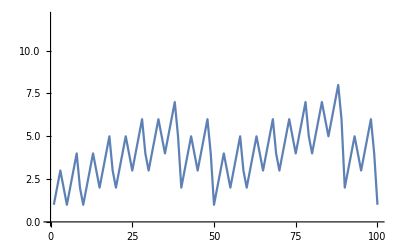

```mathematica
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}],PlotRange->Max[Table[StringLength[RomanNumeral[n]],{n,1000}]]]
```

#### +20.1 Create a list plot of Range[10] with a frame included.

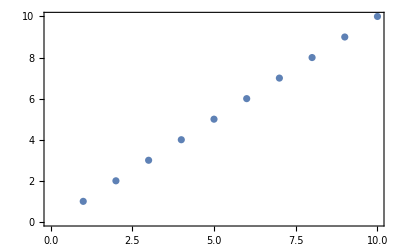

```mathematica
ListPlot[Range[10],Frame->True]
```

#### +20.2 Create a list plot of Range[10] with a yellow background and a frame.

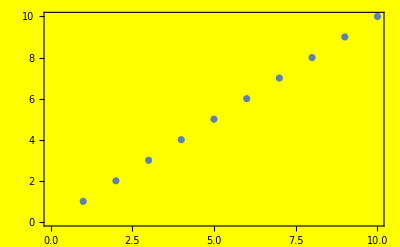

```mathematica
ListPlot[Range[10],Background->Yellow,Frame->True]
```

#### +20.3 Make a list of list plots of Range[10], with sizes ranging from 50 to 150 in steps of 10.

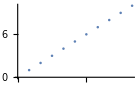
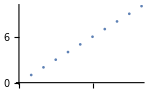
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Range[10],ImageSize->n],{n,50,150,10}]
```

#### +20.4 Make a line plot of the first 20 squares, filling to the axis.

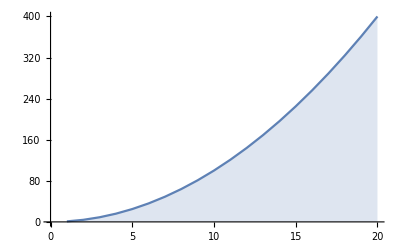

```mathematica
ListLinePlot[Table[n^2,{n,1,20}],Filling->Axis]
```

### Exercises for Section 21 | Graphs and Networks

#### 21.1 Make a graph consisting of a loop of 3 nodes.



```mathematica
Graph[{1->2,2->3,3->1}]
```

#### 21.2 Make a graph with 4 nodes in which every node is connected.

```mathematica
Graph[Flatten[Table[j->i,{i,1,4},{j,1,4}]]]
```

-Graphics-

#### 21.3 Make a table of undirected graphs with between 2 and 10 nodes in which every node is connected.

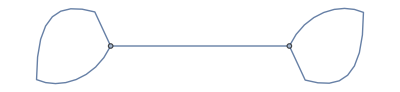
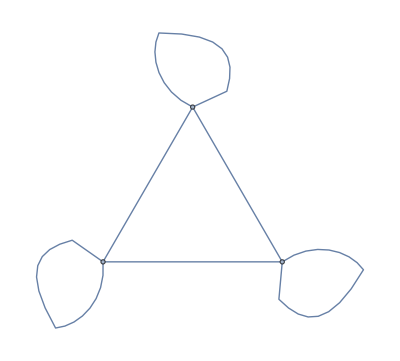
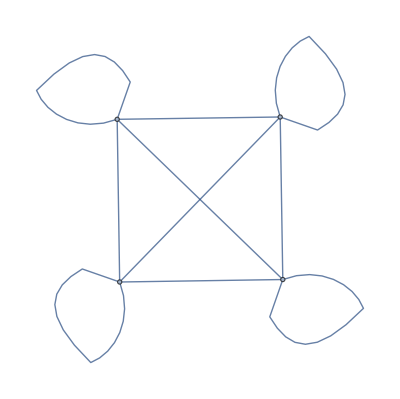
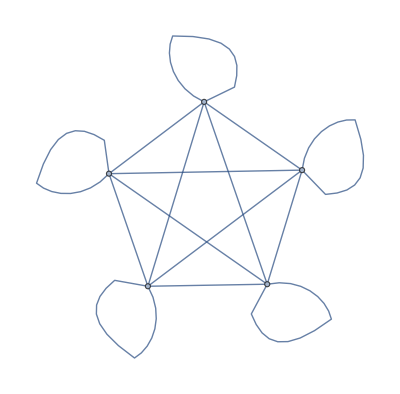
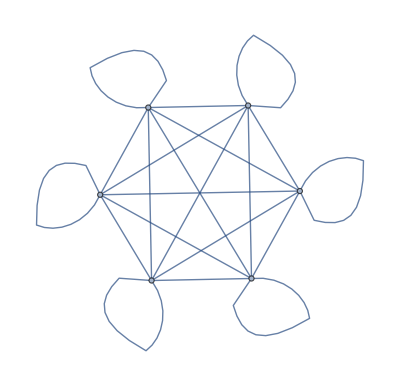
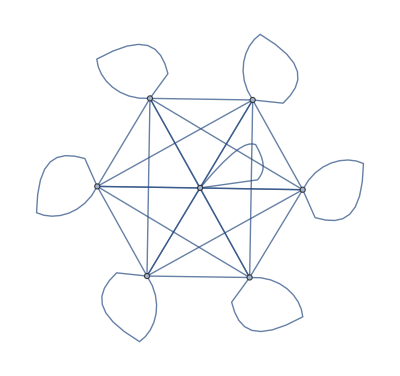
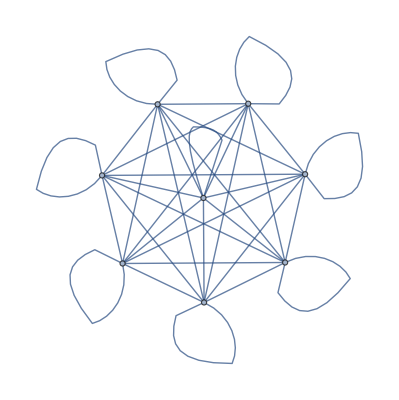
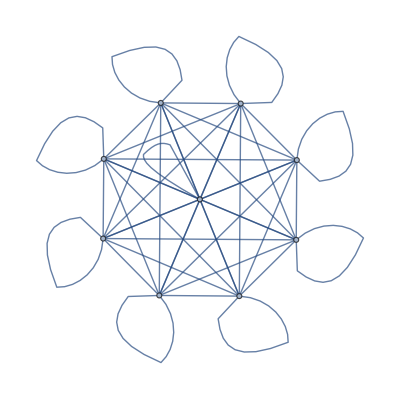

```mathematica
Table[UndirectedGraph[Flatten[Table[i->j,{i,n},{j,n}]]],{n,2,10}]
```

#### 21.4 Use Table and Flatten to get {1, 2, 1, 2, 1, 2}.

```mathematica
Flatten[Table[Table[i,{i,1,2}],3]]
```

{1,2,1,2,1,2}

#### 21.5 Make a line plot of the result of concatenating all digits of all integers from 1 to 100 (i.e. ..., 8, 9, 1, 0, 1, 1, 1, 2, ...).

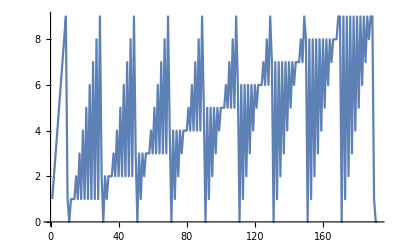

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

#### 21.6 Make a graph with 50 nodes, in which node i connects to node i + 1.

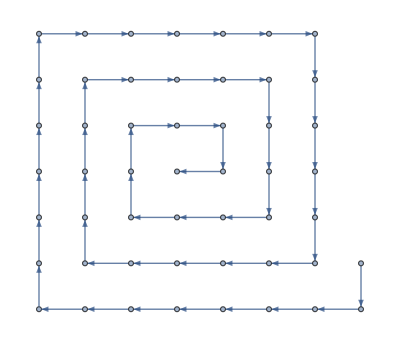

```mathematica
Graph[Table[i->i+1,{i,1,50}]]
```

#### 21.7 Make a graph with 4 nodes, in which each connection connects i to Max[i, j].

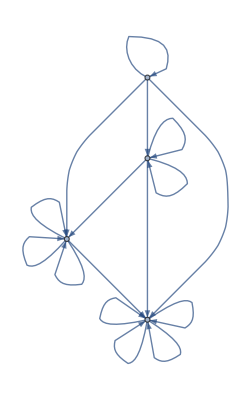

```mathematica
Graph[Flatten[Table[i->Max[i,j],{i,1,4},{j,1,4}]]]
```

#### 21.8 Make a graph in which each connection connects i to j-i, where i and j both range from 1 to 5.

```mathematica
Graph[Flatten[Table[i->(j-i),{i,1,5},{j,1,5}]]]
```

-Graphics-

#### 21.9 Generate a graph with 100 nodes, each with a connection going to one randomly chosen node.

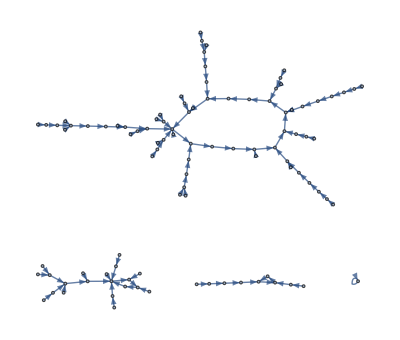

```mathematica
Graph[Table[i->RandomInteger[{1,100}],{i,1,100}]]
```

#### 21.10 Generate a graph with 100 nodes, each connection to two randomly chosen nodes.

```mathematica
Graph[Flatten[Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,1,100}]]]
```

-Graphics-

#### 21.11 For the graph {1 -> 2, 2 ->3, 3 -> 4, 4 -> 1, 3 -> 1, 2 -> 2}, make a grid giving the shortest paths between every pair of nodes, with the start node as row and end node as column.

```mathematica
Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],i,j],{i,4},{j,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

#### +21.1 Make a graph with 4 nodes in which every node is connected, displaying the resulting graph with radial drawing.

```mathematica
Graph[Flatten[Table[j->i,{i,1,4},{j,1,4}]],GraphLayout->"RadialDrawing"]
```

-Graphics-

#### +21.2 Generate a graph in which a single node is connected to 10 others.

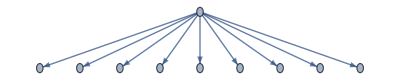

```mathematica
Graph[Table[1->i,{i,2,10}]]
```

#### +21.3 Use Flatten to generate a table of the numbers 1 to 50 in which even numbers are colored red.

```mathematica
Flatten[Table[{i,Style[i+1,Red]},{i,1,50,2}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

#### +21.4 Use ImageData, Flatten and Total to find the number of white pixels in Binarize[Rasterize[“W”]].

```mathematica
Total[Flatten[ImageData[Binarize[Rasterize["W"]]]]]
```

419

#### +21.5 Use Flatten, IntegerDigits and Total to find the sum of all digits of all whole numbers up to 1000.

```mathematica
Total[Flatten[IntegerDigits[Range[1000]]]]
```

13501

#### +21.6 Generate a graph with 200 connections, each between nodes with numbers randomly chosen between 0 and 100.

```mathematica
Graph[Table[RandomInteger[100]->RandomInteger[100],200]]
```

-Graphics-

#### +21.7 Generate a plot that shows communities in a random graph with nodes numbered between 0 and 100, and 200 connections.

```mathematica
CommunityGraphPlot[Graph[Table[RandomInteger[100]->RandomInteger[100],200]]]
```

-Graphics-

### Exercises for Section 22 | Machine Learning

#### 22.1 Identify what language the word “ajatella” comes from.

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

#### 22.2 Apply ImageIdentify to an image of a tiger, getting the image using ctrl +=.

```mathematica
ImageIdentify[Entity["Species","Species:PantheraTigris"][EntityProperty["Species","Image"]]]
```

tiger

#### 22.3 Make a table of image identifications for an image of a tiger, blurred by an amount from 1 to 5.

```mathematica
Table[ImageIdentify[Blur[LinguisticAssistant,r]],{r,1,5}]
```

{tiger,tiger,tiger,spiny-finned fish,fish}

#### 22.4 Classify the sentiment of “I’m so happy to be here”.

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

#### 22.5 Find the 10 words in WordList[] that are nearest to “happy”.

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

#### 22.6 Generate 20 random numbers up to 1000 and find which 3 are nearest to 100.

```mathematica
Nearest[RandomInteger[1000,20],100,3]
```

{103,91,65}

#### 22.7 Generate a list of 10 random colors, and find which 5 are closest to Red.

```mathematica
Nearest[RandomColor[10],Red,5]
```

{RGBColor[0.7587258613831624, 0.25904140894499483, 0.13189533056298175],RGBColor[0.6346391680248464, 0.3283204052574793, 0.20371486616697343],RGBColor[0.4067823044933587, 0.3028697342642126, 0.03084733153435315],RGBColor[0.8246325318895045, 0.37837527933389503, 0.6114825850760912],RGBColor[0.783527632998311, 0.7706063739397131, 0.5256415747636014]}

#### 22.8 Of the first 100 squares, find the one nearest to 2000.

```mathematica
Nearest[Range[100]^2,2000]
```

{2025}

#### 22.9 Find the 3 European flags nearest to the flag of Brazil.

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,6].

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Argentina"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

#### 22.10 Make a graph of the 2 nearest neighbors of each color in Table[Hue[n], {h, 0, 1, 0.05}].

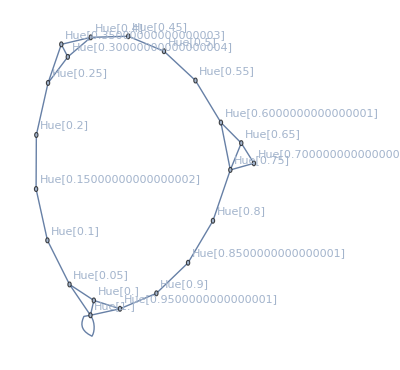

```mathematica
NearestNeighborGraph[Table[Hue[h], {h, 0, 1, 0.05}],2,VertexLabels->All]
```

#### 22.11 Generate a list of 100 random numbers from 0 to 100, and make a graph of the 2 nearest neighbors of each one.

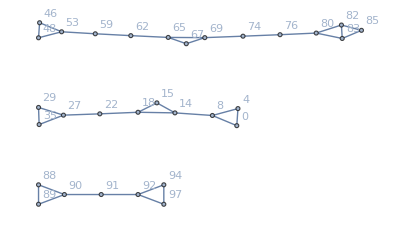

```mathematica
NearestNeighborGraph[Table[RandomInteger[100],40],2,VertexLabels->All]
```

#### 22.12 Collect the flags of Asia into clusters of similar flags.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,6].

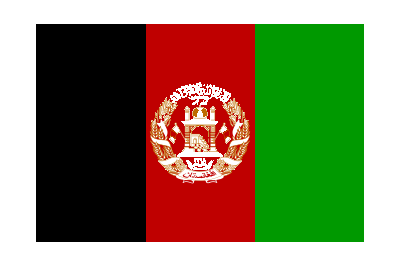
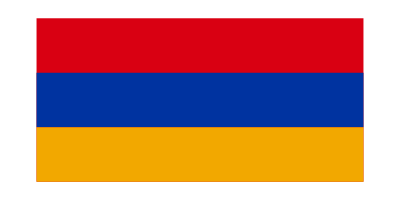
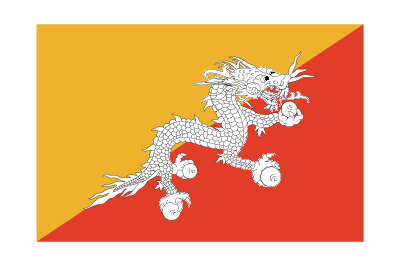

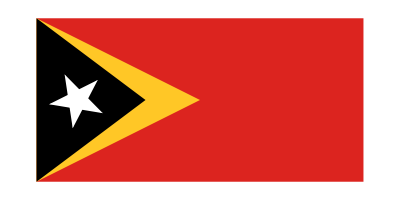
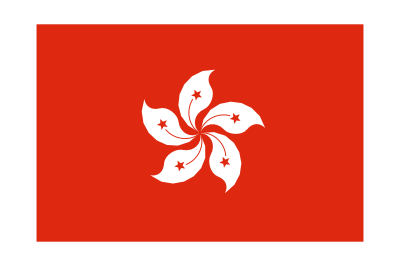
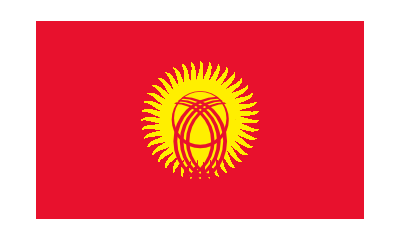
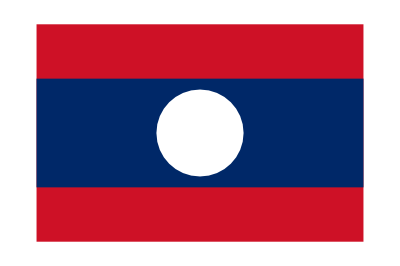
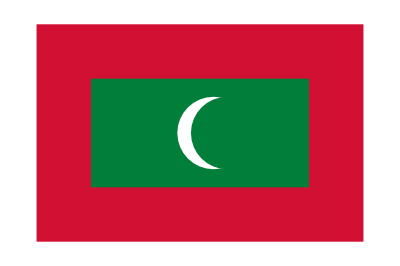
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[LinguisticAssistant]
```

#### 22.13 Make raster images of the letters of the alphabet at size 20, then make a graph of the 2 nearest neighbors of each one.

```mathematica
Table[Style[Rasterize[j],ImageSize->20],{j,Alphabet[]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Exercises for Section 23 | More about Numbers

#### 23.1 Find Sqrt(2) to 500-digit precision

```mathematica
N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

#### 23.2 Generate 10 random real numbers between 0 and 1.

```mathematica
RandomReal[1,10]
```

{0.130176,0.568446,0.725036,0.0468064,0.195519,0.447386,0.418971,0.410268,0.172226,0.844629}

#### 23.3 Make a plot of 200 points with random real x and y coordinates between 0 and 1.

```mathematica
ListPlot[Table[RandomReal[1,2],200]]
```

-Graphics-

#### 23.4 Create a random walk using AnglePath and 1000 random real numbers between 2 and 2pi.

```mathematica
Graphics[Line[AnglePath[RandomReal[{2,2Pi}, 1000]]]]
```

-Graphics-

#### 23.5 Make a table of Mod[n^2, 10] for n from 0 to 30.

```mathematica
Table[Mod[n^2,10],{n,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

#### 23.6 Make a line plot of Mod[n^n, 10] for n from 1 to 100.

```mathematica
Table[Mod[n^n,10],{n,1,100}]
```

{1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0}

#### 23.7 Make a table of the first 10 powers of pi, rounded to integers.

```mathematica
Table[Round[Power[Pi,n]],{n,1,10}]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

#### 23.8 Make a graph by connecting n with Mod[n^2, 100] for n from 0 to 99.

```mathematica
Graph[Table[n->Mod[n^2,100],{n,0,99}]]
```

-Graphics-

#### 23.9 Generate graphics of 50 circles with random real coordinates 0 to 10, random real radio from 0 to 2, and random colors.

```mathematica
Graphics[Table[Style[Circle[{RandomReal[10],RandomReal[10]},RandomReal[{0,2}]],RandomColor[]],50]]
```

-Graphics-

#### 23.10 Make a plot of the nth prime divided by n * log(n), for n from 2 to 1000.

```mathematica
ListPlot[Table[Prime[n]/(n*Log[n]),{n,2,1000}]]
```

-Graphics-

#### 23.11 Make a line plot of the differences between successive primes up to 100.

```mathematica
ListLinePlot[Table[Prime[n+1]-Prime[n],{n,1,100}]]
```

-Graphics-

#### 23.12 Generate a sequence of 20 middle C notes with random durations between 0 and 0.5 seconds.

#### 23.13 Make an array plot of Mod[i, j] for i and j up to 50.

#### 23.14 Make a list for n from 2 to 10 of array plots for x and y up to 50 of x^y mod n.

#### +23.1 Use Round to compute the fractional part of pi to 50 digits.

#### +23.2 Find the sum of the first 1000 prime numbers.

#### +23.3 Make a list of the first 100 primes modulo 4.

#### +23.4 Make a list of the first 10000 primers modulo 4, multiply them by 90 degrees and create an angle path from them.